# Even-point Multi-loop Unitarity and its Applications

JJM Carrasco, NH Pavao
2307.16812

## Background

## Some Functions

### Bubble and Triangle

```mathematica
triangleI[Subscript[α, 1],Subscript[α, 2],Subscript[α, 3],{0}]/.Ds-> 2Ds
```

(ⅈ^(1-2 Ds) 2^(-2 Ds) π^-Ds Sij^(Ds-α_1-α_2-α_3) Gamma[Ds-α_1-α_2] Gamma[Ds-α_2-α_3] Gamma[-Ds+α_1+α_2+α_3])/(Gamma[α_1] Gamma[2 Ds-α_1-α_2-α_3] Gamma[α_3])

```mathematica
bubbleI[Subscript[α, 1],Subscript[α, 2],{0}]/.Ds-> 2Ds
```

(ⅈ^(1-2 Ds) 2^(-2 Ds) π^-Ds Sij^(Ds-α_1-α_2) Gamma[Ds-α_1] Gamma[Ds-α_2] Gamma[-Ds+α_1+α_2])/(Gamma[α_1] Gamma[2 Ds-α_1-α_2] Gamma[α_2])

```mathematica
bubbleI[a_,b_,{r_}]:=I/(-4*Pi)^(Ds/2)(Gamma[a+b-(Ds+2r)/2]Gamma[(Ds+2r)/2-b]Gamma[(Ds+2r)/2-a])/(Gamma[a]Gamma[b]Gamma[Ds-a-b])(Sij)^((Ds+2r)/2-a-b)(Gamma[(Ds-4)+r])/(2^r Gamma[(Ds-4)])
```

```mathematica
triangleI[a_,b_,c_,{r_}]:=I/(-4*Pi)^(Ds/2)(Gamma[a+b+c-(Ds+2r)/2]Gamma[(Ds+2r)/2-b-c]Gamma[(Ds+2r)/2-a-b])/(Gamma[a]Gamma[c]Gamma[(Ds+2r)-a-b-c])Sij^((Ds+2r)/2-a-b-c)(Gamma[(Ds-4)+r])/(2^r Gamma[(Ds-4)])
```

```mathematica
bubbleI[a_,b_]:=bubbleI[a,b,{0}]
```

```mathematica
triangleI[a_,b_,c_]:=triangleI[a,b,c,{0}]
```

```mathematica
Series[triangleI[a,0,c]/bubbleI[a,c]/.Ds-> 4-2ϵ,{ϵ,0,3}]
```

1

### Rest

```mathematica
getSystem[expression_]:=Last/@ArrayRules[Last[CoefficientArrays[expression,Union[extractType[expression,blp]]]]]
```

```mathematica
Attributes[blp]={Orderless}
```

{Orderless}

```mathematica
{{blp[0,0]:=0}, {}, {blp[-a_,b_]:=-blp[a,b]}, {}, {blp[a_+b_,c_]:=blp[a,c]+blp[b,c]}, {}, {blp[a_,b_ d_?NumberQ]:=d blp[a,b]}, {}, {blp[a_,√λ b_]:=√λ blp[a,b]}, {}, {blp[a_,b_/g]:=blp[a,b]/g}}
```

{{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null}}

```mathematica
extractType[data_,head_]:=Flatten[Last[Reap[data/.head[a___]:>Sow[head[a]]]]]
```

```mathematica
kinBasisTree={blp[k[2,0],ϵ[k[1,0]]]->-blp[k[3,0],ϵ[k[1,0]]]-blp[k[4,0],ϵ[k[1,0]]],blp[k[1,0],ϵ[k[1,0]]]->0,blp[k[2,0],ϵ[k[2,0]]]->0,blp[k[1,0],ϵ[k[2,0]]]->-blp[k[3,0],ϵ[k[2,0]]]-blp[k[4,0],ϵ[k[2,0]]],blp[k[3,0],ϵ[k[3,0]]]->0,blp[k[1,0],ϵ[k[3,0]]]->-blp[k[2,0],ϵ[k[3,0]]]-blp[k[4,0],ϵ[k[3,0]]],blp[k[4,0],ϵ[k[4,0]]]->0,blp[k[1,0],ϵ[k[4,0]]]->-blp[k[2,0],ϵ[k[4,0]]]-blp[k[3,0],ϵ[k[4,0]]],blp[k[4,0],k[4,0]]->0,blp[k[3,0],k[3,0]]->0,blp[k[2,0],k[3,0]]->-blp[k[2,0],k[4,0]]-blp[k[3,0],k[4,0]],blp[k[2,0],k[2,0]]->0,blp[k[1,0],k[4,0]]->-blp[k[2,0],k[4,0]]-blp[k[3,0],k[4,0]],blp[k[1,0],k[3,0]]->blp[k[2,0],k[4,0]],blp[k[1,0],k[2,0]]->blp[k[3,0],k[4,0]],blp[k[1,0],k[1,0]]->0};
```

```mathematica
kinBasis1loop={blp[k[1,0],l[1,0]]->-blp[k[2,0],l[1,0]]-blp[k[3,0],l[1,0]]-blp[k[4,0],l[1,0]],blp[k[2,0],ϵ[k[1,0]]]->-blp[k[3,0],ϵ[k[1,0]]]-blp[k[4,0],ϵ[k[1,0]]],blp[k[1,0],ϵ[k[1,0]]]->0,blp[k[2,0],ϵ[k[2,0]]]->0,blp[k[1,0],ϵ[k[2,0]]]->-blp[k[3,0],ϵ[k[2,0]]]-blp[k[4,0],ϵ[k[2,0]]],blp[k[3,0],ϵ[k[3,0]]]->0,blp[k[1,0],ϵ[k[3,0]]]->-blp[k[2,0],ϵ[k[3,0]]]-blp[k[4,0],ϵ[k[3,0]]],blp[k[4,0],ϵ[k[4,0]]]->0,blp[k[1,0],ϵ[k[4,0]]]->-blp[k[2,0],ϵ[k[4,0]]]-blp[k[3,0],ϵ[k[4,0]]],blp[k[4,0],k[4,0]]->0,blp[k[3,0],k[3,0]]->0,blp[k[2,0],k[3,0]]->-blp[k[2,0],k[4,0]]-blp[k[3,0],k[4,0]],blp[k[2,0],k[2,0]]->0,blp[k[1,0],k[4,0]]->-blp[k[2,0],k[4,0]]-blp[k[3,0],k[4,0]],blp[k[1,0],k[3,0]]->blp[k[2,0],k[4,0]],blp[k[1,0],k[2,0]]->blp[k[3,0],k[4,0]],blp[k[1,0],k[1,0]]->0};
```

```mathematica
ProjectorFreeQ[l_]:={blp[a___,ϵ[l],b___] c___ blp[d___,ϵ[-l],f___]:>(c (blp[a,b,d,f]-(blp[a,b,l] blp[d,f,q[1,0]]+blp[f,d,l] blp[b,a,q[1,0]])/blp[l,q[First[l],0]])//Together),blp[ϵ[l],ϵ[-l]]:>Ds[1]-2}
```

```mathematica
ProjectorFixedQ[l_]:={blp[a___,ϵ[l],b___] c___ blp[d___,ϵ[-l],f___]:>c blp[a,b,d,f],blp[ϵ[l],ϵ[-l]]:>Ds[1]}
```

```mathematica
lorentzProd[list1_,list2_]:=(First@list1)(First@list2)-(Rest@list1).(Rest@list2);
```

```mathematica
constructOnShellNull[nPoint_,dDim_]:=Module[{trialList},trialList=Table[Module[{threeMom},threeMom=(RandomReal[1,WorkingPrecision->60]&)/@Range[dDim-1];Join[{√Total[Thread[threeMom threeMom]]},threeMom]],{i,1,nPoint-2}];trialList=Append[trialList,-((Flatten[{1,(0&)/@Range[dDim-2],1}] lorentzProd[Total[trialList],Total[trialList]])/lorentzProd[Flatten[{2,(0&)/@Range[dDim-2],2}],Total[trialList]])];trialList=Append[trialList,Total[-trialList]]]
```

```mathematica
evaluateIn4D[amp_,polList_,fedMoms_]:=Module[{momenta,symbols,value},symbols=(k[#1,0]&)/@Range[Length[polList]];momenta=fedMoms;value=Simplify[Expand[amp/.Thread[ϵ/@symbols->Thread[ϵ[symbols,polList]]]/.{blp[k[a___],k[b___]]:>1/2 ab[k[a],k[b]] sb[k[b],k[a]],blp[k[a___],ϵ[k[b___],p]]:>(ab[q,k[a]] sb[k[a],k[b]])/(√2 ab[q,k[b]]),blp[k[a___],ϵ[k[b___],m]]:>-(sb[q,k[a]] ab[k[a],k[b]])/(√2 sb[q,k[b]]),blp[ϵ[k[a___],m],ϵ[k[b___],m]]:>0,blp[ϵ[k[b___],p],ϵ[k[a___],p]]:>0,blp[ϵ[k[b___],p],ϵ[k[a___],m]]:>-(ab[q,k[a]] sb[q,k[b]])/(ab[q,k[b]] sb[q,k[a]]),blp[ϵ[k[b___],m],ϵ[k[b___],p]]:>-(ab[q,k[b]] sb[q,k[a]])/(ab[q,k[a]] sb[q,k[b]])}/.q->{5,4,3,0}/.Thread[(k[#1,0]&)/@Range[Length[fedMoms]]->momenta]/.evaluateSH]];value]
```

```mathematica
evaluateSH:={ab[a_,b_]:>((a⟦2⟧+ⅈ a⟦3⟧) (b⟦1⟧+b⟦4⟧)-(b⟦2⟧+ⅈ b⟦3⟧) (a⟦1⟧+a⟦4⟧))/(√(a⟦1⟧+a⟦4⟧) √(b⟦1⟧+b⟦4⟧)),sb[a_,b_]:>((b⟦2⟧-ⅈ b⟦3⟧) (a⟦1⟧+a⟦4⟧)-(a⟦2⟧-ⅈ a⟦3⟧) (b⟦1⟧+b⟦4⟧))/(√(a⟦1⟧+a⟦4⟧) √(b⟦1⟧+b⟦4⟧))}
```

## Vector Building Blocks

### Background Functions

```mathematica
nScal["dd1"][a_,b_,c_,d_]:=2blp[k[a,0],k[b,0]]
```

```mathematica
nScal["dd2"][a_,b_,c_,d_]:=(2blp[k[a,0],k[c,0]])(2blp[k[a,0],k[d,0]])
```

```mathematica
nVec["F4"][a_,b_,c_,d_]:=F[a,b,c,d]
```

```mathematica
nVec["F2F2"][a_,b_,c_,d_]:=F[a,b]F[c,d]
```

```mathematica
nVec["YM+F3"][a_,b_,c_,d_]:=2 (-2 blp[k[3,0],ϵ[k[2,0]]] blp[k[3,0],ϵ[k[4,0]]] blp[k[4,0],ϵ[k[1,0]]] blp[k[4,0],ϵ[k[3,0]]]+blp[k[2,0],k[4,0]] blp[k[3,0],ϵ[k[4,0]]] blp[k[4,0],ϵ[k[3,0]]] blp[ϵ[k[1,0]],ϵ[k[2,0]]]+blp[k[3,0],k[4,0]] blp[k[3,0],ϵ[k[4,0]]] blp[k[4,0],ϵ[k[3,0]]] blp[ϵ[k[1,0]],ϵ[k[2,0]]]-blp[k[2,0],k[4,0]] blp[k[3,0],ϵ[k[4,0]]] blp[k[4,0],ϵ[k[2,0]]] blp[ϵ[k[1,0]],ϵ[k[3,0]]]-blp[k[3,0],k[4,0]] blp[k[3,0],ϵ[k[4,0]]] blp[k[4,0],ϵ[k[2,0]]] blp[ϵ[k[1,0]],ϵ[k[3,0]]]+blp[k[2,0],k[4,0]] blp[k[3,0],ϵ[k[2,0]]] blp[k[4,0],ϵ[k[3,0]]] blp[ϵ[k[1,0]],ϵ[k[4,0]]]+blp[k[3,0],k[4,0]] blp[k[3,0],ϵ[k[2,0]]] blp[k[4,0],ϵ[k[3,0]]] blp[ϵ[k[1,0]],ϵ[k[4,0]]]+blp[k[2,0],k[4,0]] blp[k[3,0],ϵ[k[1,0]]] blp[k[3,0],ϵ[k[4,0]]] blp[ϵ[k[2,0]],ϵ[k[3,0]]]+blp[k[3,0],k[4,0]] blp[k[3,0],ϵ[k[1,0]]] blp[k[3,0],ϵ[k[4,0]]] blp[ϵ[k[2,0]],ϵ[k[3,0]]]+2 blp[k[3,0],k[4,0]] blp[k[3,0],ϵ[k[4,0]]] blp[k[4,0],ϵ[k[1,0]]] blp[ϵ[k[2,0]],ϵ[k[3,0]]]+blp[k[2,0],ϵ[k[4,0]]] (blp[k[3,0],ϵ[k[2,0]]] (-2 blp[k[4,0],ϵ[k[1,0]]] blp[k[4,0],ϵ[k[3,0]]]+(blp[k[2,0],k[4,0]]+blp[k[3,0],k[4,0]]) blp[ϵ[k[1,0]],ϵ[k[3,0]]])+(blp[k[2,0],k[4,0]]+blp[k[3,0],k[4,0]]) (blp[k[4,0],ϵ[k[3,0]]] blp[ϵ[k[1,0]],ϵ[k[2,0]]]-blp[k[4,0],ϵ[k[2,0]]] blp[ϵ[k[1,0]],ϵ[k[3,0]]])+((blp[k[2,0],k[4,0]]+blp[k[3,0],k[4,0]]) blp[k[3,0],ϵ[k[1,0]]]+(-blp[k[2,0],k[4,0]]+blp[k[3,0],k[4,0]]) blp[k[4,0],ϵ[k[1,0]]]) blp[ϵ[k[2,0]],ϵ[k[3,0]]])-blp[k[2,0],k[4,0]] blp[k[4,0],ϵ[k[1,0]]] blp[k[4,0],ϵ[k[3,0]]] blp[ϵ[k[2,0]],ϵ[k[4,0]]]-blp[k[3,0],k[4,0]] blp[k[4,0],ϵ[k[1,0]]] blp[k[4,0],ϵ[k[3,0]]] blp[ϵ[k[2,0]],ϵ[k[4,0]]]-2 blp[k[2,0],k[4,0]] blp[k[3,0],k[4,0]] blp[ϵ[k[1,0]],ϵ[k[3,0]]] blp[ϵ[k[2,0]],ϵ[k[4,0]]]-2 blp[k[3,0],k[4,0]]^2 blp[ϵ[k[1,0]],ϵ[k[3,0]]] blp[ϵ[k[2,0]],ϵ[k[4,0]]]+blp[k[2,0],ϵ[k[3,0]]] (2 blp[k[3,0],ϵ[k[1,0]]] blp[k[3,0],ϵ[k[2,0]]] blp[k[3,0],ϵ[k[4,0]]]+2 blp[k[3,0],ϵ[k[2,0]]] blp[k[3,0],ϵ[k[4,0]]] blp[k[4,0],ϵ[k[1,0]]]+2 blp[k[3,0],ϵ[k[4,0]]] blp[k[4,0],ϵ[k[1,0]]] blp[k[4,0],ϵ[k[2,0]]]+2 blp[k[2,0],ϵ[k[4,0]]] (blp[k[3,0],ϵ[k[1,0]]] blp[k[3,0],ϵ[k[2,0]]]+blp[k[4,0],ϵ[k[1,0]]] blp[k[4,0],ϵ[k[2,0]]])-blp[k[2,0],k[4,0]] blp[k[3,0],ϵ[k[4,0]]] blp[ϵ[k[1,0]],ϵ[k[2,0]]]-blp[k[3,0],k[4,0]] blp[k[3,0],ϵ[k[4,0]]] blp[ϵ[k[1,0]],ϵ[k[2,0]]]+blp[k[2,0],k[4,0]] blp[k[3,0],ϵ[k[2,0]]] blp[ϵ[k[1,0]],ϵ[k[4,0]]]-blp[k[3,0],k[4,0]] blp[k[3,0],ϵ[k[2,0]]] blp[ϵ[k[1,0]],ϵ[k[4,0]]]-blp[k[2,0],k[4,0]] blp[k[4,0],ϵ[k[2,0]]] blp[ϵ[k[1,0]],ϵ[k[4,0]]]-blp[k[3,0],k[4,0]] blp[k[4,0],ϵ[k[2,0]]] blp[ϵ[k[1,0]],ϵ[k[4,0]]]+(blp[k[2,0],k[4,0]]+blp[k[3,0],k[4,0]]) (blp[k[3,0],ϵ[k[1,0]]]-blp[k[4,0],ϵ[k[1,0]]]) blp[ϵ[k[2,0]],ϵ[k[4,0]]])+(blp[k[2,0],k[4,0]]+blp[k[3,0],k[4,0]]) (blp[k[3,0],ϵ[k[1,0]]] blp[k[3,0],ϵ[k[2,0]]]+blp[k[4,0],ϵ[k[1,0]]] (2 blp[k[3,0],ϵ[k[2,0]]]+blp[k[4,0],ϵ[k[2,0]]])+2 blp[k[2,0],k[4,0]] blp[ϵ[k[1,0]],ϵ[k[2,0]]]) blp[ϵ[k[3,0]],ϵ[k[4,0]]])/.Thread[{k[4,0],k[1,0],k[2,0],k[3,0]}-> {k[a,0],k[b,0],k[c,0],k[d,0]}];
```

### Numerators

```mathematica
Clear[nS,nT,nU]
```

Adjoint Numerators

```mathematica
{nS["YM+F3"],nT["YM+F3"],nU["YM+F3"]}={nVec["YM+F3"][1,2,3,4],nVec["YM+F3"][4,1,2,3],nVec["YM+F3"][1,3,2,4]};
```

```mathematica
nS["YM+F3"]-nT["YM+F3"]-nU["YM+F3"]/.kinBasisTree//Expand
```

0

Symmetric Vector Numerators

```mathematica
{nS["F2F2"],nT["F2F2"],nU["F2F2"]}={nVec["F2F2"][1,2,3,4],nVec["F2F2"][4,1,2,3],nVec["F2F2"][1,3,2,4]};
```

```mathematica
{nS["F4"],nT["F4"],nU["F4"]}={nVec["F4"][1,3,2,4],nVec["F4"][1,2,4,3],nVec["F4"][1,2,3,4]};
```

Symmetric Scalar Numerators

```mathematica
{nS["dd1"],nT["dd1"],nU["dd1"]}={nScal["dd1"][1,2,3,4],nScal["dd1"][4,1,2,3],nScal["dd1"][1,3,2,4]};
```

```mathematica
{nS["dd2"],nT["dd2"],nU["dd2"]}={nScal["dd2"][1,2,3,4],nScal["dd2"][4,1,2,3],nScal["dd2"][1,3,2,4]};
```

### Spanning Set of 4-point Operators

```mathematica
With[{n=2},Table[α^(n)Subscript[a, x,n-2x]^("F2F2")((nS["dd1"])^(x+1)(nS["dd2"])^ (n-2x) nS["F2F2"]+(nT["dd1"])^(x+1)(nT["dd2"])^(n-2x) nT["F2F2"]+(nU["dd1"])^(x+1)(nU["dd2"])^(n-2x)  nU["F2F2"])+α^(n)Subscript[a, x,n-2x]^("F4")((nS["dd1"])^(x+1)(nS["dd2"])^ (n-2x) nS["F4"]+(nT["dd1"])^(x+1)(nT["dd2"])^(n-2x) nT["F4"]+(nU["dd1"])^(x+1)(nU["dd2"])^(n-2x)  nU["F4"]),{x,0,Floor[n/2]}]];
```

## Background Data

```mathematica
s[a_,b_]:=blp[k[a,0]+k[b,0],k[a,0]+k[b,0]];
```

```mathematica
kinBasis={blp[k[2],ϵ[k[1]]]->-blp[k[3],ϵ[k[1]]]-blp[k[4],ϵ[k[1]]],blp[k[1],ϵ[k[1]]]->0,blp[k[2],ϵ[k[2]]]->0,blp[k[1],ϵ[k[2]]]->-blp[k[3],ϵ[k[2]]]-blp[k[4],ϵ[k[2]]],blp[k[3],ϵ[k[3]]]->0,blp[k[1],ϵ[k[3]]]->-blp[k[2],ϵ[k[3]]]-blp[k[4],ϵ[k[3]]],blp[k[4],ϵ[k[4]]]->0,blp[k[1],ϵ[k[4]]]->-blp[k[2],ϵ[k[4]]]-blp[k[3],ϵ[k[4]]],blp[k[4],k[4]]->0,blp[k[3],k[3]]->0,blp[k[2],k[3]]->-blp[k[2],k[4]]-blp[k[3],k[4]],blp[k[2],k[2]]->0,blp[k[1],k[4]]->-blp[k[2],k[4]]-blp[k[3],k[4]],blp[k[1],k[3]]->blp[k[2],k[4]],blp[k[1],k[2]]->blp[k[3],k[4]],blp[k[1],k[1]]->0};
```

```mathematica
coeff[b_,c_,d_,e_]:=-(s12 coeff[1+b,1+c,-1+d,e])/(2 (-1+b+c+d)+Ds);
coeff[b_,c_,0,e_]:=(-1-(2 c)/(-4+2 b+Ds)) (coeff[-1+b,c,0,-1+e]/s12+coeff[-1+b,c,0,e]);
coeff[0,c_,0,e_]:=coeff[0,-1+c,0,-1+e]/s12;
coeff[0,0,0,e_]:=int[3,e];
```

```mathematica
coeff[m_,0]:=-((Ds+2 (m-2)) coeff[m-1,0])/(2 (Ds+m-3));
coeff[0,0]:=int[2];
coeff[m_,k_]:=-((2 s12) coeff[m+2,k-1])/(2 (Ds+2 (m+k-1)));
```

```mathematica
F[a_,b_]:=blp[k[a],ϵ[k[b]]] blp[k[b],ϵ[k[a]]]-blp[k[a],k[b]] blp[ϵ[k[a]],ϵ[k[b]]]
```

```mathematica
F[a_,b_,c_,d_]:=blp[k[a],ϵ[k[b]]] blp[k[b],ϵ[k[c]]] blp[k[c],ϵ[k[d]]] blp[k[d],ϵ[k[a]]]+blp[k[a],ϵ[k[d]]] blp[k[b],ϵ[k[a]]] blp[k[c],ϵ[k[b]]] blp[k[d],ϵ[k[c]]]+blp[k[a],ϵ[k[d]]] blp[k[b],ϵ[k[c]]] blp[k[c],k[d]] blp[ϵ[k[a]],ϵ[k[b]]]-blp[k[a],k[d]] blp[k[b],ϵ[k[c]]] blp[k[c],ϵ[k[d]]] blp[ϵ[k[a]],ϵ[k[b]]]-blp[k[a],ϵ[k[d]]] blp[k[b],k[c]] blp[k[d],ϵ[k[c]]] blp[ϵ[k[a]],ϵ[k[b]]]-blp[k[a],ϵ[k[b]]] blp[k[b],ϵ[k[c]]] blp[k[c],k[d]] blp[ϵ[k[a]],ϵ[k[d]]]+blp[k[a],ϵ[k[b]]] blp[k[b],k[c]] blp[k[d],ϵ[k[c]]] blp[ϵ[k[a]],ϵ[k[d]]]-blp[k[a],k[b]] blp[k[c],ϵ[k[b]]] blp[k[d],ϵ[k[c]]] blp[ϵ[k[a]],ϵ[k[d]]]-blp[k[a],ϵ[k[d]]] blp[k[b],ϵ[k[a]]] blp[k[c],k[d]] blp[ϵ[k[b]],ϵ[k[c]]]+blp[k[a],k[d]] blp[k[b],ϵ[k[a]]] blp[k[c],ϵ[k[d]]] blp[ϵ[k[b]],ϵ[k[c]]]-blp[k[a],k[b]] blp[k[c],ϵ[k[d]]] blp[k[d],ϵ[k[a]]] blp[ϵ[k[b]],ϵ[k[c]]]+blp[k[a],k[b]] blp[k[c],k[d]] blp[ϵ[k[a]],ϵ[k[d]]] blp[ϵ[k[b]],ϵ[k[c]]]-blp[k[a],k[d]] blp[k[b],ϵ[k[a]]] blp[k[c],ϵ[k[b]]] blp[ϵ[k[c]],ϵ[k[d]]]-blp[k[a],ϵ[k[b]]] blp[k[b],k[c]] blp[k[d],ϵ[k[a]]] blp[ϵ[k[c]],ϵ[k[d]]]+blp[k[a],k[b]] blp[k[c],ϵ[k[b]]] blp[k[d],ϵ[k[a]]] blp[ϵ[k[c]],ϵ[k[d]]]+blp[k[a],k[d]] blp[k[b],k[c]] blp[ϵ[k[a]],ϵ[k[b]]] blp[ϵ[k[c]],ϵ[k[d]]]
```

```mathematica
kinBasis1loop={blp[k[1],l[1]]->-blp[k[2],l[1]]-blp[k[3],l[1]]-blp[k[4],l[1]],blp[k[2],ϵ[k[1]]]->-blp[k[3],ϵ[k[1]]]-blp[k[4],ϵ[k[1]]],blp[k[1],ϵ[k[1]]]->0,blp[k[2],ϵ[k[2]]]->0,blp[k[1],ϵ[k[2]]]->-blp[k[3],ϵ[k[2]]]-blp[k[4],ϵ[k[2]]],blp[k[3],ϵ[k[3]]]->0,blp[k[1],ϵ[k[3]]]->-blp[k[2],ϵ[k[3]]]-blp[k[4],ϵ[k[3]]],blp[k[4],ϵ[k[4]]]->0,blp[k[1],ϵ[k[4]]]->-blp[k[2],ϵ[k[4]]]-blp[k[3],ϵ[k[4]]],blp[k[4],k[4]]->0,blp[k[3],k[3]]->0,blp[k[2],k[3]]->-blp[k[2],k[4]]-blp[k[3],k[4]],blp[k[2],k[2]]->0,blp[k[1],k[4]]->-blp[k[2],k[4]]-blp[k[3],k[4]],blp[k[1],k[3]]->blp[k[2],k[4]],blp[k[1],k[2]]->blp[k[3],k[4]],blp[k[1],k[1]]->0};
```

## Building the integrand

First, we want a function that grabs the different four-point amplitudes needed for integrand construction in this paper:

```mathematica
constructOnShellNull[nPoint_,dDim_]:=Module[{trialList},trialList=Table[Module[{threeMom},threeMom=(RandomReal[1,WorkingPrecision-> 60]&)/@Range[dDim-1];Join[{√Total[Thread[threeMom threeMom]]},threeMom]],{i,1,nPoint-2}];trialList=Append[trialList,-((Flatten[{1,(0&)/@Range[dDim-2],1}] lorentzProd[Total[trialList],Total[trialList]])/lorentzProd[Flatten[{2,(0&)/@Range[dDim-2],2}],Total[trialList]])];trialList=Append[trialList,Total[-trialList]]]
```

Here are some 4-point kinematics we can play around with

```mathematica
(vectors[#]=constructOnShellNull[4,4])&/@Range@10;
```

```mathematica
treeAmp[labels_,momenta_]:=amp[labels]/.Thread[(k/@Range@(momenta//Length))-> momenta];
```

```mathematica
kitchenSinkStateSum[amp_]:=orderColor[colorSum[gaugeFixedPolSum[Expand[gammaExpand[spinorSum[amp//Expand]]]]]];
```

```mathematica
spinorSum[amp_]:=(amp)//.{c___  gammaString[d___,v[-l[a_]]]gammaString[u[l[a_]],b___]:>c gammaString[First[{d}],Join[Last[{d}],{l[a]},First[{b}]],Last[{b}]],c___  gammaString[d___,v[l[a_]]]gammaString[u[-l[a_]],b___]:>c gammaString[First[{d}],Join[Last[{d}],{-l[a]},First[{b}]],Last[{b}]],

c___  gammaString[d___,v[-l[a_]]]gammaString[b___,u[l[a_]]]:>c gammaString[First[{d}],Join[Last[{d}],{l[a]},First[{b}//Reverse]],Last[{b}//Reverse]],c___  gammaString[d___,v[l[a_]]]gammaString[b___,u[-l[a_]]]:>c gammaString[First[{d}],Join[Last[{d}],{-l[a]},First[{b}//Reverse]],Last[{b}//Reverse]],

c___  gammaString[v[-l[a_]],d___]gammaString[u[l[a_]],b___]:>c gammaString[First[{d}//Reverse],Join[Last[{d}//Reverse],{l[a]},First[{b}]],Last[{b}]],c___  gammaString[v[l[a_]],d___]gammaString[u[-l[a_]],b___]:>c gammaString[First[{d}//Reverse],Join[Last[{d}//Reverse],{-l[a]},First[{b}]],Last[{b}]],

c___  gammaString[v[-l[a_]],d___]gammaString[b___,u[l[a_]]]:>c gammaString[First[{d}//Reverse],Join[Last[{d}//Reverse],{l[a]},First[{b}//Reverse]],Last[{b}//Reverse]],
c___  gammaString[v[l[a_]],d___]gammaString[b___,u[-l[a_]]]:>c gammaString[First[{d}//Reverse],Join[Last[{d}//Reverse],{-l[a]},First[{b}//Reverse]],Last[{b}//Reverse]],

gammaString[u[-l[a_]],{b___},v[l[a_]]]:>gammaString[Join[{b},{-l[a]}]],gammaString[u[l[a_]],{b___},v[-l[a_]]]:>gammaString[Join[{b},{l[a]}]],gammaString[v[-l[a_]],{b___},u[l[a_]]]:>gammaString[Join[{b}//Reverse,{l[a]}]],gammaString[v[l[a_]],{b___},u[-l[a_]]]:>gammaString[Join[{b}//Reverse,{-l[a]}]]}
```

```mathematica
colorSum[amp_]:=(amp//Expand)//.{d___ color[e___ ,l[a_]]color[-l[a_],f___]:>d color[e,f],d___ color[f___,-l[a_]]color[l[a_],e___]:>d color[f,e],d___ color[l[a_],e___ ]color[f___,-l[a_]]:>d color[f,e],d___ color[-l[a_],f___]color[e___,l[a_]]:>d color[e,f],d___ color[l[a_],e___ ]color[-l[a_],f___]:>d color@@Join[{e}//Reverse,{f}],d___ color[-l[a_],f___]color[l[a_],e___]:>d color@@Join[{f}//Reverse,{e}],d___ color[e___ ,l[a_]]color[f___,-l[a_]]:>d color@@Join[{f}//Reverse,{e}],d___ color[f___,-l[a_]]color[e___,l[a_]]:>d color@@Join[{e}//Reverse,{f}],d___ color[l[a_],b___,-l[a_]]:>d color[b],d___ color[-l[a_],b___,l[a_]]:>d color[b]}
```

```mathematica
orderColor[amp_]:=amp/.color[a___,k[1],b___]:>If[1===(Signature@{b,a}),color[k[1],b,a],color@@Join[{k[1]},{b,a}//Reverse]]
```

```mathematica
gaugeFixedPolSum[amp_]:=amp//.{blp[a___,ϵ[l[e_]]] c___ blp[d___,ϵ[-l[e_]]]:>c blp[a,d],blp[ϵ[l[e_]],ϵ[-l[e_]]]:>Ds[1]}
```

```mathematica
gaugePolSum[amp_]:=amp//.{d___ blp[a___,ϵ[l[b_]]]blp[c___,ϵ[-l[b_]]]:>(d(blp[a,c]-(blp[q,a]blp[l[b],c]+blp[q,c]blp[l[b],a])/blp[q,l[b]])//Expand),d___ blp[ϵ[-l[b_]],ϵ[l[b_]]]:>(d (Ds[1]-2)//Expand)}
```

```mathematica
lorentzContract[amp_]:=Expand[amp]//.{blp[a___,μ[b_]] blp[μ[b_],c___]:>blp[a,c],blp[a___,μ[b_]]^2:>blp[a,a],blp[a___,MU[b_]] blp[MU[b_],c___]:>blp[a,c],blp[a___,MU[b_]]^2:>blp[a,a],blp[ϵ[k[a___]],μ[b_]] parityTrace[d___,μ[b_],c___]:>parityTrace[d,ϵ[k[a]],c],blp[k[a_],μ[b_]] parityTrace[d___,μ[b_],c___]:>parityTrace[d,k[a],c],blp[μ[a_],μ[b_]] parityTrace[d___,μ[b_],c___]:>parityTrace[d,μ[a],c],blp[MU[a_],μ[b_]] parityTrace[d___,μ[b_],c___]:>parityTrace[d,MU[a],c],blp[MU[a_],MU[a_]]:>Ds[1],blp[μ[a_],μ[a_]]:>Ds[1]};
```

```mathematica
gammaContract[gammaString_]:=Module[{listOfgammas,newList},listOfgammas=List@@gammaString;If[Length[listOfgammas]==2,newList=blp@@First/@listOfgammas,newList=Total[Table[(-1)^i blp[First[listOfgammas⟦1⟧],First[listOfgammas⟦i⟧]] gS@@(Rest[listOfgammas]/.{a___,listOfgammas⟦i⟧,b___}:>{a,b}),{i,2,Length[gammaString]}]]];newList/.{gS[a___]:>gammaContract[gs[a]]}]
```

```mathematica
gammaExpand[amp_]:=amp/.gammaString[a___]:>g[Ds]lorentzContract[((Times@@MapIndexed[blp[#1,μ[#2//First]]&,a])((gammaString@@γ[μ[#]]&/@Range@Length@a)//gammaContract)//Expand)]
```

```mathematica
gammaExpandOdd4D[amp_]:=amp/.gammaString[a___]:>lorentzContract[((Times@@MapIndexed[blp[#1,μ[#2//First]]&,a])((gammaString@@γ[μ[#]]&/@Range@Length@a)//gammaContractOdd4D)//Expand)]
```

```mathematica
gammaContractOdd4D[gammaString_]:=Module[{listOfgammas,newList},listOfgammas=List@@gammaString;If[Length[listOfgammas]==4,newList=parityTrace@@First/@listOfgammas,newList=Total[Table[(-1)^i blp[First[listOfgammas⟦1⟧],First[listOfgammas⟦i⟧]] gS@@(Rest[listOfgammas]/.{a___,listOfgammas⟦i⟧,b___}:>{a,b}),{i,2,Length[gammaString]}]]];newList/.{gS[a___]:>gammaContractOdd4D[gs[a]]}]
```

```mathematica
evaluateIn4D[amp_,polList_,fedMoms_]:=Module[{momenta,symbols,value},symbols=(k[#1,0]&)/@Range[Length[polList]];momenta=fedMoms;value=amp/.Thread[ϵ/@symbols->Thread[ϵ[symbols,polList]]]/.{blp[k[a___],k[b___]]:>1/2 ab[k[a],k[b]] sb[k[b],k[a]],

blp[k[a___],ϵ[k[b___],p]]:>(ab[q,k[a]] sb[k[a],k[b]])/(√2 ab[q,k[b]]),

blp[k[a___],ϵ[k[b___],m]]:>-(sb[q,k[a]] ab[k[a],k[b]])/(√2 sb[q,k[b]]),

blp[ϵ[k[a___],m],ϵ[k[b___],m]]:>0,

blp[ϵ[k[b___],p],ϵ[k[a___],p]]:>0,

blp[ϵ[k[b___],p],ϵ[k[a___],m]]:>-(ab[q,k[a]] sb[q,k[b]])/(ab[q,k[b]] sb[q,k[a]]),

parityTrace[a1_,b1_,c1_,d1_]:>(p[R]ab[a1,b1]sb[b1,c1]ab[c1,d1]sb[d1,a1]+p[L]sb[a1,b1]ab[b1,c1]sb[c1,d1]ab[d1,a1]),

blp[ϵ[k[a___],m],ϵ[k[b___],p]]:>-(ab[q,k[b]] sb[q,k[a]])/(ab[q,k[a]] sb[q,k[b]])}//.{ab[a___,ϵ[k[b_,0],m],c___]:>-Sqrt[2]ab[a,k[b,0],c],ab[a___,ϵ[k[b_,0],p],c___]:>ab[a,q,c]/ab[q,k[b,0]],sb[a___,ϵ[k[b_,0],p],c___]:>Sqrt[2]sb[a,k[b,0],c],sb[a___,ϵ[k[b_,0],m],c___]:>sb[a,q,c]/sb[q,k[b,0]]}
/.q->{5,4,3,0}/.Thread[(k[#1,0]&)/@Range[Length[fedMoms]]->momenta]/.evaluateSH//Expand//Simplify;value]
```

## Amplitudes from paper

### mixed particle amps

```mathematica
amp[{l1,g,X1,l1}]:=(blp[k[1],k[3]]gammaString[u[k[1]],{ϵ[k[2]],k[1]+k[2]},v[k[4]]]+blp[k[1],k[2]]gammaString[u[k[1]],{k[1]+k[3],ϵ[k[2]]},v[k[4]]]);
```

```mathematica
amp[{lV,g,g,lV}]:=I(blp[k[1],k[3]]gammaString[v[k[1]],{ϵ[k[2]],k[1]+k[2],ϵ[k[3]]},v[k[4]]]+blp[k[1],k[2]]gammaString[v[k[1]],{ϵ[k[3]],k[1]+k[3],ϵ[k[2]]},v[k[4]]]);
```

```mathematica
amp[{lU,g,g,lU}]:=I(blp[k[1],k[3]]gammaString[u[k[1]],{ϵ[k[2]],k[1]+k[2],ϵ[k[3]]},u[k[4]]]+blp[k[1],k[2]]gammaString[u[k[1]],{ϵ[k[3]],k[1]+k[3],ϵ[k[2]]},u[k[4]]]);
```

```mathematica
amp[{l1,g,g,l1}]:=(blp[k[1],k[3]]gammaString[u[k[1]],{ϵ[k[2]],k[1]+k[2],ϵ[k[3]]},v[k[4]]]+blp[k[1],k[2]]gammaString[u[k[1]],{ϵ[k[3]],k[1]+k[3],ϵ[k[2]]},v[k[4]]]);

amp[{X1,g,g,X1}]:=-(4blp[k[1],k[2]]blp[k[4],ϵ[k[2]]]blp[k[1],ϵ[k[3]]]+4blp[k[1],k[3]]blp[k[1],ϵ[k[2]]]blp[k[4],ϵ[k[3]]]+2blp[k[1],k[3]]2blp[k[1],k[2]]blp[ϵ[k[2]],ϵ[k[3]]])
```

```mathematica
amp[{l1,l2,l2,l1}]:=blp[k[1],k[2]]gammaString[u[k[1]],{MU[10]},v[k[4]]]gammaString[u[k[3]],{MU[10]},v[k[2]]];
```

```mathematica
amp[{X1,X2,X2,X1}]:=-2blp[k[1],k[2]]2blp[k[1],k[3]];
```

```mathematica
amp[{l1,X1,X1,l1}]:=(blp[k[1],k[3]]gammaString[u[k[1]],{k[1]+k[2]},v[k[4]]]+blp[k[1],k[2]]gammaString[u[k[1]],{k[1]+k[3]},v[k[4]]]);
```

```mathematica
amp[{lU,X1,X1,lU}]:=(blp[k[1],k[3]]gammaString[u[k[1]],{k[1]+k[2]},u[k[4]]]+blp[k[1],k[2]]gammaString[u[k[1]],{k[1]+k[3]},u[k[4]]]);
```

```mathematica
amp[{lV,X1,X1,lV}]:=(blp[k[1],k[3]]gammaString[v[k[1]],{k[1]+k[2]},v[k[4]]]+blp[k[1],k[2]]gammaString[v[k[1]],{k[1]+k[3]},v[k[4]]]);
```

```mathematica
amp[{sG,sG,sG,sG}]:=2blp[k[1],k[2]]2blp[k[1],k[3]]2blp[k[1],k[4]];
```

### same particle amps

```mathematica
amp[{g,g,g,g}]:=2(F[1,2,3,4]-F[1,2]F[3,4]+F[1,3,4,2]-F[1,3]F[4,2]+F[1,4,2,3]-F[1,4]F[2,3]);
```

```mathematica
amp[{lU,lU,lV,lV}]:=2(blp[k[1],k[3]]gammaString[u[k[1]],{MU[10]},v[k[4]]]gammaString[u[k[2]],{MU[10]},v[k[3]]]+pm[1]blp[k[1],k[4]]gammaString[u[k[1]],{MU[10]},v[k[3]]]gammaString[u[k[2]],{MU[10]},v[k[4]]]);
```

```mathematica
amp[{l1,l1,l1,l1}]:=2(blp[k[1],k[3]]gammaString[u[k[1]],{MU[10]},v[k[2]]]gammaString[u[k[3]],{MU[10]},v[k[4]]]+blp[k[1],k[2]]gammaString[u[k[1]],{MU[10]},v[k[4]]]gammaString[u[k[3]],{MU[10]},v[k[2]]]);
```

```mathematica
amp[{X1,X1,X1,X1}]:=(2blp[k[1],k[3]])^2;
```

```mathematica
amp[{π,π,π,π}]:=2blp[k[1],k[3]]color[k[1],k[2],k[3],k[4]]+2blp[k[1],k[2]]color[k[1],k[3],k[2],k[4]];
```

This is the wrong counterterm to plug in -- needs to be fixed.

```mathematica
amp[{G,G,G,G}]:=A[1](nS["dd1"]^2F[1,2]F[3,4]+nU["dd1"]^2F[1,3]F[2,4]+nT["dd1"]^2F[1,4]F[3,2])/.k[a_,0]:>k[a];
```

## Results

## Cuts

### 1-loop bubble

#### Sewing code

```mathematica
bubRules1loop={blp[k[2],ϵ[k[1]]]->-blp[k[3],ϵ[k[1]]]-blp[k[4],ϵ[k[1]]],blp[k[1],ϵ[k[1]]]->0,blp[k[2],ϵ[k[2]]]->0,blp[k[1],ϵ[k[2]]]->-blp[k[3],ϵ[k[2]]]-blp[k[4],ϵ[k[2]]],blp[k[3],ϵ[k[3]]]->0,blp[k[1],ϵ[k[3]]]->-blp[k[2],ϵ[k[3]]]-blp[k[4],ϵ[k[3]]],blp[k[4],ϵ[k[4]]]->0,blp[k[1],ϵ[k[4]]]->-blp[k[2],ϵ[k[4]]]-blp[k[3],ϵ[k[4]]],blp[k[4],k[4]]->0,blp[k[3],k[3]]->0,blp[k[2],k[2]]->0,blp[k[2],k[3]]->-blp[k[2],k[4]]-blp[k[3],k[4]],blp[k[1],k[4]]->-blp[k[2],k[4]]-blp[k[3],k[4]],blp[k[1],k[3]]->blp[k[2],k[4]],blp[k[1],k[2]]->blp[k[3],k[4]],blp[k[3],l[1]]->blp[k[3],k[4]]-blp[k[4],l[1]],blp[k[1],l[1]]->-blp[k[2],l[1]]-blp[k[3],k[4]],blp[l[1],l[1]]->0,blp[k[1],k[1]]->0};
```

```mathematica
sewAmps1loop[treeAmps_]:=Module[{cutKinRules,sewnAmps},
cutKinRules=(Join[(blp[l[#],l[#]]==0&/@Range@2)/.l[2]-> -l[1]-k[1]-k[2]/.kinBasis1loop,kinBasis1loop/.{(a___-> b___):>a==b}]/.k[a_]:>q[a]//Reduce//ToRules)/.q[a_]:>k[a];
sewnAmps=treeAmps[[1]]treeAmps[[2]]/.atree-> treeAmp//kitchenSinkStateSum;
sewnAmps/.l[2]-> -l[1]-k[1]-k[2]/.cutKinRules//Expand//lorentzContract];
```

#### Pions

```mathematica
loopRulesBub={blp[k[2],ϵ[k[1]]]->-blp[k[3],ϵ[k[1]]]-blp[k[4],ϵ[k[1]]],blp[k[1],ϵ[k[1]]]->0,blp[k[2],ϵ[k[2]]]->0,blp[k[1],ϵ[k[2]]]->-blp[k[3],ϵ[k[2]]]-blp[k[4],ϵ[k[2]]],blp[k[3],ϵ[k[3]]]->0,blp[k[1],ϵ[k[3]]]->-blp[k[2],ϵ[k[3]]]-blp[k[4],ϵ[k[3]]],blp[k[4],ϵ[k[4]]]->0,blp[k[1],ϵ[k[4]]]->-blp[k[2],ϵ[k[4]]]-blp[k[3],ϵ[k[4]]],blp[k[4],k[4]]->0,blp[k[3],k[3]]->0,blp[k[2],k[2]]->0,blp[k[2],k[3]]->-blp[k[2],k[4]]-blp[k[3],k[4]],blp[k[1],k[4]]->-blp[k[2],k[4]]-blp[k[3],k[4]],blp[k[1],k[3]]->blp[k[2],k[4]],blp[k[1],k[2]]->blp[k[3],k[4]],blp[k[3],l[1]]->blp[k[3],k[4]]-blp[k[4],l[1]],blp[k[1],l[1]]->-blp[k[2],l[1]]-blp[k[3],k[4]],blp[l[1],l[1]]->0,blp[k[1],k[1]]->0};
```

```mathematica
pionCut1loop=sewAmps1loop[{atree[{π,π,π,π},{l[1],k[1],k[2],l[2]}],atree[{π,π,π,π},{-l[2],k[3],k[4],-l[1]}]}];
```

#### 𝒩 ≤ 1 DBIVA

```mathematica
vectorCut1loopHD=sewAmps1loop[{atree[{G,G,G,G},{l[1],k[1],k[2],l[2]}],atree[{g,g,g,g},{-l[2],k[3],k[4],-l[1]}]}];
```

```mathematica
vectorCut1loop=sewAmps1loop[{atree[{g,g,g,g},{l[1],k[1],k[2],l[2]}],atree[{g,g,g,g},{-l[2],k[3],k[4],-l[1]}]}];
```

```mathematica
fermCut1loop=sewAmps1loop[{atree[{l1,g,g,l1},{l[1],k[1],k[2],l[2]}],atree[{l1,g,g,l1},{-l[2],k[3],k[4],-l[1]}]}];
scalarCut1loop=sewAmps1loop[{atree[{X1,g,g,X1},{l[1],k[1],k[2],l[2]}],atree[{X1,g,g,X1},{-l[2],k[3],k[4],-l[1]}]}];
```

### 2-loop double bubble

#### Sewing code

```mathematica
sewAmps2loopAlmost[treeAmps_]:=Module[{cutKinRules,sewnAmps,momAssign},momAssign=If[MemberQ[((#~extractType~l//Union//Length)&/@treeAmps),4],{l[2]->-l[1]-k[3]-k[4],l[3]->-l[4]-k[1]-k[2]},{l[2]->-l[1]-k[3]-k[4],l[3]->k[2]+l[4]-l[1]}];
cutKinRules=(Join[(kinBasis/.Thread[(k/@Range@4)->(#//Last)])&/@treeAmps//Flatten,kinBasis]/.{blp[b___,ϵ[l[a_]]]:>0,blp[b___,ϵ[-l[a_]]]:>0}/.momAssign/.{(a___->b___):>a==b}/.k[a_]:>q[a]//Reduce//ToRules)/.q[a_]:>k[a];
sewnAmps=treeAmps[[1]] treeAmps[[2]] treeAmps[[3]]/.atree->treeAmp//Expand;
ParallelSum[kitchenSinkStateSum[expr]/.momAssign/.cutKinRules//Expand//lorentzContract,{expr,List@@sewnAmps}]]
```

```mathematica
kitchenSinkStateSum[amp_]:=orderColor[colorSum[gaugeFixedPolSum[Expand[gammaExpand[spinorSum[Expand[amp]]]]]]]
```

```mathematica
sewAmps2loop[treeAmps_]:=Module[{cutKinRules,sewnAmps,momAssign},

momAssign=If[MemberQ[((#~extractType~l//Union//Length)&/@treeAmps),4],{l[2]-> -l[1]-k[3]-k[4],l[3]-> -l[4]-k[1]-k[2]},{l[2]-> -l[1]-k[3]-k[4],l[3]-> k[2]+l[4]-l[1]}];

cutKinRules=(Join[(kinBasis/.Thread[(k/@Range@4)-> (#//Last)])&/@treeAmps//Flatten,kinBasis]/.{blp[b___,ϵ[l[a_]]]:>0,blp[b___,ϵ[-l[a_]]]:>0}/.momAssign/.{(a___-> b___):>a==b}/.k[a_]:>q[a]//Reduce//ToRules)/.q[a_]:>k[a];

sewnAmps=treeAmps[[1]]treeAmps[[2]]treeAmps[[3]]/.atree-> treeAmp//kitchenSinkStateSum;

(sewnAmps/.momAssign/.cutKinRules//Expand//lorentzContract)]
```

#### Pions

```mathematica
pionCut2loopBub=8(doubleBox[{1,2},{3,4}](blp[k[1],l[3]]blp[l[1],l[3]]blp[k[3],l[1]]+blp[k[1],l[3]]blp[l[2],l[3]]blp[k[3],l[2]]+blp[k[2],l[3]]blp[l[2],l[3]]blp[k[3],l[1]]+blp[k[2],l[3]]blp[l[1],l[3]]blp[k[3],l[2]])+doubleBox[{1,2},{4,3}](blp[k[2],l[3]]blp[l[2],l[3]]blp[k[3],l[2]]+blp[k[2],l[3]]blp[l[1],l[3]]blp[k[3],l[1]]+blp[k[1],l[3]]blp[l[2],l[3]]blp[k[3],l[1]]+blp[k[1],l[3]]blp[l[1],l[3]]blp[k[3],l[2]]))/.{l[2]-> -l[1]-k[3]-k[4],l[3]->- l[4]-k[1]-k[2]};
```

```mathematica
N4Cut2loopBub=(2blp[k[1],k[2]])^4 d8[Q]/.{l[2]-> -l[1]-k[3]-k[4],l[3]-> -l[4]-k[1]-k[2]};
```

```mathematica
bubRules2loop={blp[k[1],ϵ[k[1]]]->0,blp[k[2],ϵ[k[2]]]->0,blp[k[3],ϵ[k[3]]]->0,blp[k[4],ϵ[k[4]]]->0,blp[k[2],ϵ[k[1]]]->-blp[k[3],ϵ[k[1]]]-blp[k[4],ϵ[k[1]]],blp[k[1],ϵ[k[2]]]->-blp[k[3],ϵ[k[2]]]-blp[k[4],ϵ[k[2]]],blp[k[1],ϵ[k[3]]]->-blp[k[2],ϵ[k[3]]]-blp[k[4],ϵ[k[3]]],blp[k[1],ϵ[k[4]]]->-blp[k[2],ϵ[k[4]]]-blp[k[3],ϵ[k[4]]],blp[k[4],k[4]]->0,blp[k[3],k[3]]->0,blp[k[2],k[3]]->-blp[k[2],k[4]]-blp[k[3],k[4]],blp[k[2],k[2]]->0,blp[k[1],k[4]]->-blp[k[2],k[4]]-blp[k[3],k[4]],blp[k[1],k[3]]->blp[k[2],k[4]],blp[k[1],k[2]]->blp[k[3],k[4]],blp[k[1],k[1]]->0,blp[k[3],l[4]]->blp[k[3],k[4]]-blp[k[4],l[4]],blp[k[1],l[4]]->-blp[k[2],l[4]]-blp[k[3],k[4]],blp[l[4],l[4]]->0,blp[k[3],l[1]]->-blp[k[3],k[4]]-blp[k[4],l[1]],blp[k[1],l[1]]->-blp[k[2],l[1]]+blp[k[3],k[4]],blp[l[1],l[1]]->0};
```

#### 𝒩 = 0 DBIVA

```mathematica
{timing[1],Cut2loopBub[1]}=sewAmps2loop[{atree[{g,g,g,g},{l[4],k[1],k[2],l[3]}],atree[{g,g,g,g},{-l[4],-l[1],-l[2],-l[3]}],atree[{g,g,g,g},{l[2],k[3],k[4],l[1]}]}]//Timing;
```

```mathematica
BIDoubleBubble=Cut2loopBub[1];
```

```mathematica
sGalDoubleBubble=(sewAmps2loop[{atree[{sG,sG,sG,sG},{l[4],k[1],k[2],l[3]}],atree[{sG,sG,sG,sG},{-l[4],-l[1],-l[2],-l[3]}],atree[{sG,sG,sG,sG},{l[2],k[3],k[4],l[1]}]}]//Simplify);
```

```mathematica
N4Cut2loopBub=(2blp[k[1],k[2]])^4 d8[Q]/.{l[2]-> -l[1]-k[3]-k[4],l[3]-> -l[4]-k[1]-k[2]};
```

```mathematica
Save["/Users/nicpavao/Dropbox/2loopNLSM/2loopNLSM/evenPointCuts.m",{BIDoubleBubble,N4DBIVADoubleBubble,sGalDoubleBubble}]
```

### 2-loop dunce cap

#### Pions

Since the state sum is trivial for NLSM pions, we just give the cuts from the paper below:

```mathematica
pionCut2loopDunce= 8(crossBox[{1,2},3,4]((blp[k[1],l[3]] blp[k[2],l[3]]+blp[k[1],l[4]] blp[k[2],l[4]]) (blp[k[3],l[1]]+blp[k[3],l[2]]))-(blp[k[1],l[4]] blp[k[2],l[3]] +blp[k[1],l[3]] blp[k[2],l[4]] )(blp[k[3],l[1]] doubleBox[{1,2},{3,4}]+blp[k[3],l[2]] doubleBox[{1,2},{4,3}])/.{l[2]-> -l[1]-k[3]-k[4],l[3]-> k[2]+l[4]-l[1]});
```

```mathematica
N4Cut2loopDunce=(2blp[k[1],k[2]])^2 (blp[k[1]-l[2],k[1]-l[2]])^2 d8[Q]/.{l[2]-> -l[1]-k[3]-k[4],l[3]-> k[2]+l[4]-l[1]};
```

```mathematica
dunceRules2loop={blp[k[3],ϵ[k[3]]]->0,blp[k[4],ϵ[k[4]]]->0,blp[k[2],ϵ[k[2]]]->0,blp[k[1],ϵ[k[1]]]->0,blp[k[1],k[1]]->0,blp[k[2],ϵ[k[1]]]->-blp[k[3],ϵ[k[1]]]-blp[k[4],ϵ[k[1]]],blp[k[1],ϵ[k[2]]]->-blp[k[3],ϵ[k[2]]]-blp[k[4],ϵ[k[2]]],blp[k[1],ϵ[k[3]]]->-blp[k[2],ϵ[k[3]]]-blp[k[4],ϵ[k[3]]],blp[k[1],ϵ[k[4]]]->-blp[k[2],ϵ[k[4]]]-blp[k[3],ϵ[k[4]]],blp[k[4],k[4]]->0,blp[k[3],k[3]]->0,blp[k[2],k[3]]->-blp[k[2],k[4]]-blp[k[3],k[4]],blp[k[2],k[2]]->0,blp[k[1],k[4]]->-blp[k[2],k[4]]-blp[k[3],k[4]],blp[k[1],k[3]]->blp[k[2],k[4]],blp[k[1],k[2]]->blp[k[3],k[4]],blp[k[1],l[4]]->-blp[k[2],l[4]]-blp[k[3],l[4]]-blp[k[4],l[4]],blp[l[4],l[4]]->0,blp[k[3],l[1]]->-blp[k[3],k[4]]-blp[k[4],l[1]],blp[k[1],l[1]]->-blp[k[2],l[1]]+blp[k[3],k[4]],blp[l[1],l[4]]->-blp[k[2],l[1]]+blp[k[2],l[4]],blp[l[1],l[1]]->0};
```

#### 𝒩 = 0 DBIVA

```mathematica
Cut2loopDunce[1]=sewAmps2loop[{atree[{g,g,g,g},{l[1],k[3],k[4],l[2]}],atree[{g,g,g,g},{k[2],l[4],-l[3],-l[1]}],atree[{g,g,g,g},{k[1],-l[4],l[3],-l[2]}]}];
```

```mathematica
BIOstrich=Cut2loopDunce[1];
```

```mathematica
N4DBIVAOstrich=N4Cut2loopDunce;
```

```mathematica
sGalBIOstrich=(sewAmps2loop[{atree[{sG,sG,sG,sG},{l[1],k[3],k[4],l[2]}],atree[{sG,sG,sG,sG},{k[2],l[4],-l[3],-l[1]}],atree[{sG,sG,sG,sG},{k[1],-l[4],l[3],-l[2]}]}]//Simplify);
```

```mathematica
Save["/Users/nicpavao/Dropbox/2loopNLSM/2loopNLSM/evenPointCuts.m",{BIOstrich,N4DBIVAOstrich,sGalBIOstrich}];
```

### Other cuts NOT in paper for general SUSY (**don’t run these**)

#### 𝒩 ≥ 1 DBIVA

```mathematica
t1=2blp[k[1],-l[1]-k[1]-k[2]];
t2=2blp[k[1],l[1]];
t3=2blp[l[1],-l[2]-k[1]-k[2]];
t4=2blp[l[1],l[2]];
t5=2blp[l[2],-l[3]-k[1]-k[2]];
t6=2blp[l[2],l[3]];
t7=2blp[l[3],k[3]];
t8=2blp[l[3],k[4]];
```

```mathematica
Series[integrateBubble[integrateBubble[t1 t3 t5+t1 t4 t6 +t2 t4 t5 +t2 t3 t6 ,l[1],k[1]+k[2]]/.l[3]-> k[4],l[2],k[1]+k[2]]/.Ds-> 2-2ϵ//Expand//FullSimplify,{ϵ,0,0}]
```

8 blp[k[2],k[4]] blp[k[3],k[4]]^2 int[2]^2+O[ϵ]^1

```mathematica
Series[integrateBubble[integrateBubble[integrateBubble[t1 t3 t5 t7+t1 t4 t6 t7+t1 t4 t5 t8+t1 t3 t6 t8+t2 t3 t5 t8+t2 t3 t6 t7+t2 t4 t5 t7+t2 t4 t6 t8,l[1],k[1]+k[2]],l[2],k[1]+k[2]],l[3],k[1]+k[2]]/.Ds-> 2-2ϵ//Expand//FullSimplify,{ϵ,0,0}]
```

16 blp[k[2],k[4]] blp[k[3],k[4]]^3 int[2]^3+O[ϵ]^1

```mathematica
Series[Sij triangleI[1,2ϵ,1]/.Ds-> 2-2ϵ,{ϵ,0,-1}]
```

ⅈ/(9 π ϵ)+O[ϵ]^0

```mathematica
Series[bubbleI[1,1]/.Ds-> 2-2ϵ,{ϵ,0,-1}]
```

ⅈ/(2 π Sij ϵ)+O[ϵ]^0

```mathematica
Cut2loopDunce[2]=sewAmps2loopAlmost[{atree[{g,g,g,g},{l[1],k[3],k[4],l[2]}],atree[{l1,g,g,l1},{-l[3],k[2],-l[1],l[4]}],atree[{l1,g,g,l1},{-l[4],k[1],-l[2],l[3]}]}];
```

```mathematica
Cut2loopDunce[3]=sewAmps2loopAlmost[{atree[{l1,g,g,l1},{l[1],k[3],k[4],l[2]}],atree[{l1,g,g,l1},{l[4],k[2],-l[3],-l[1]}],atree[{l1,g,g,l1},{-l[2],k[1],l[3],-l[4]}]}];
```

```mathematica
Cut2loopDunce[4]=sewAmps2loop[{atree[{X1,g,g,X1},{l[1],k[3],k[4],l[2]}],atree[{X1,g,g,X1},{l[4],k[2],-l[3],-l[1]}],atree[{X1,g,g,X1},{-l[2],k[1],l[3],-l[4]}]}];
```

```mathematica
Cut2loopDunce[5]=sewAmps2loop[{atree[{g,g,g,g},{l[1],k[3],k[4],l[2]}],atree[{X1,g,g,X1},{-l[3],k[2],-l[1],l[4]}],atree[{X1,g,g,X1},{-l[4],k[1],-l[2],l[3]}]}];
```

```mathematica
Cut2loopDunce[6]=sewAmps2loop[{atree[{X1,g,g,X1},{l[1],k[3],k[4],l[2]}],atree[{l1,g,X1,l1},{-l[3],k[2],-l[1],l[4]}],atree[{l1,g,X1,l1},{-l[4],k[1],-l[2],l[3]}]}];
```

```mathematica
Cut2loopDunce[7]=sewAmps2loop[{atree[{l1,g,g,l1},{l[1],k[3],k[4],l[2]}],atree[{l1,g,X1,l1},{l[4],k[2],-l[3],-l[1]}],atree[{l1,g,X1,l1},{-l[2],k[1],l[3],-l[4]}]}];
```

#### 𝒩 ≥ 1 DBIVA

```mathematica
{timing[2],Cut2loopBub[2]}=sewAmps2loopAlmost[{atree[{l1,g,g,l1},{l[4],k[1],k[2],l[3]}],atree[{l1,g,g,l1},{-l[3],-l[1],-l[2],-l[4]}],atree[{g,g,g,g},{l[1],k[3],k[4],l[2]}]}]//Timing;
```

```mathematica
{timing[3],Cut2loopBub[3]}=sewAmps2loopAlmost[{atree[{lV,g,g,lV},{l[3],k[1],k[2],l[4]}],atree[{lU,lU,lV,lV},{-l[3],-l[4],-l[1],-l[2]}],atree[{lU,g,g,lU},{l[1],k[3],k[4],l[2]}]}]//Timing;
```

```mathematica
{timing[3],Cut2loopBub[3]}=sewAmps2loopAlmost[{atree[{l1,g,g,l1},{l[3],k[1],k[2],l[4]}],atree[{l1,l1,l1,l1},{-l[4],-l[1],-l[2],-l[3]}],atree[{l1,g,g,l1},{l[1],k[3],k[4],l[2]}]}]//Timing;
```

```mathematica
Cut2loopBub[4]=sewAmps2loop[{atree[{X1,g,g,X1},{l[4],k[1],k[2],l[3]}],atree[{X1,X2,X2,X1},{-l[4],-l[1],-l[2],-l[3]}],atree[{X1,g,g,X1},{l[2],k[3],k[4],l[1]}]}];
```

```mathematica
Cut2loopBub[5]=sewAmps2loop[{atree[{X1,g,g,X1},{l[4],k[1],k[2],l[3]}],atree[{X1,X1,X1,X1},{-l[4],-l[1],-l[2],-l[3]}],atree[{X1,g,g,X1},{l[2],k[3],k[4],l[1]}]}];
```

```mathematica
Cut2loopBub[6]=sewAmps2loop[{atree[{l1,g,g,l1},{l[3],k[1],k[2],l[4]}],atree[{l1,l2,l2,l1},{-l[4],-l[1],-l[2],-l[3]}],atree[{l1,g,g,l1},{l[1],k[3],k[4],l[2]}]}];
```

```mathematica
Cut2loopBub[7]=sewAmps2loop[{atree[{X1,g,g,X1},{l[4],k[1],k[2],l[3]}],atree[{X1,g,g,X1},{-l[4],-l[1],-l[2],-l[3]}],atree[{g,g,g,g},{l[2],k[3],k[4],l[1]}]}];
```

```mathematica
Cut2loopBub[8]=sewAmps2loop[{atree[{X1,g,g,X1},{l[4],k[1],k[2],l[3]}],atree[{l1,X1,X1,l1},{-l[1],-l[4],-l[3],-l[2]}],atree[{l1,g,g,l1},{l[2],k[3],k[4],l[1]}]}];
```

#### 𝒩 ≥ 2 DBIVA

```mathematica
scalarCut1loop=sewAmps1loop[{atree[{X1,g,g,X1},{l[1],k[1],k[2],l[2]}],atree[{X1,g,g,X1},{-l[2],k[3],k[4],-l[1]}]}];
```

```mathematica
scalarCut1loopA=sewAmps1loop[{atree[{X1,g,g,X1},{k[1],l[1],k[2],l[2]}],atree[{X1,g,g,X1},{k[3],-l[2],k[4],-l[1]}]}];
```

## Integrals

### Integrals

#### Integral Code

```mathematica
pullLoopMomFromTrace[amp_]:=Module[{loopsInTrace,iter,newExpand},loopsInTrace=(amp~extractType~parityTrace)~extractType~l;
newExpand=amp;
For[i=1,i<1+(Length@loopsInTrace),i++,newExpand=newExpand/.(d___ parityTrace[a___,loopsInTrace[[i]],b___]:>d parityTrace[a,MU[i],b]blp[loopsInTrace[[i]],MU[i]])];
newExpand]
```

```mathematica
LoopToTensor[term_,loop_]:=Module[{loopTerms,nonLoopTerms},loopTerms=Select[term,!Length[extractType[#1/.loop-> tag[loop],tag]]==0&];If[!Length[loopTerms]===0,loopTerms=(#1/.{blp[loop,a___]^b_:>(blp[a,loop]&)/@Range[b],blp[a___,loop]^b_:>(blp[a,loop]&)/@Range[b]}&)/@List@@(hold loopTerms);loopTerms=Times@@MapIndexed[#1/.{blp[a___,loop]:>blp[a,μ[First@#2]]}&,Flatten[
Rest[loopTerms]]]];nonLoopTerms=Select[term,Length[extractType[#1/.loop-> tag[loop],tag]]==0&];loopTerms nonLoopTerms]
```

```mathematica
symmetricTensor[kA_,metB_]:=Union[(Times@@Flatten[{hold/@#1⟦1;;kA⟧/.{hold[a_]:>blp[K12,a]},hold/@Partition[#1⟦kA+1;;All⟧,2]/.hold[{μ[a_],μ[b_]}]:>blp[μ[a],μ[b]]}]&)/@Permutations[μ[#]&/@Range[kA+2 metB]]]
```

```mathematica
symmetricTensor[kA_,kB_,metC_]:=Union[(Times@@Flatten[{hold/@#1⟦1;;kA⟧/.{hold[a_]:>blp[K1,a]},hold/@#1⟦kA+1;;kB+kA⟧/.{hold[a_]:>blp[K2,a]},hold/@Partition[#1⟦kA+kB+1;;All⟧,2]/.hold[{μ[a_],μ[b_]}]:>blp[μ[a],μ[b]]}]&)/@Permutations[(μ[#]&)/@Range[kA+kB+2 metC]]]
```

```mathematica
integrateBubble[integrand_,loopMom_,scale_]:=(integrateBubbleTensor[LoopToTensor[#,loopMom]]&/@(integrand//Expand))/.K12-> scale/.c-> coeff/.s12-> blp[scale,scale]/.Ds[1]-> Ds/.kinBasis;
```

```mathematica
paramListTriangle[n_]:=Table[c[m,n-2k-m,k,ϵ],{k,0,Floor[n/2]},{m,0,n-2k}]//Flatten
```

```mathematica
paramListBubble[n_]:=Table[c[n-2k,k],{k,0,Floor[n/2]}]
```

```mathematica
integrateBubbleTensor[tensorFormTerm_]:=Module[{powerOfLoop},powerOfLoop=Length[extractType[tensorFormTerm,μ]];lorentzContract[Expand[Total[tensorFormTerm Flatten[paramListBubble[powerOfLoop]/.c[a_,b_]:>c[a,b] symmetricTensor[a,b]]]]]/.kinBasis]
```

```mathematica
integrateTriangleTensor[tensorFormTerm_]:=Module[{powerOfLoop},powerOfLoop=Length[extractType[tensorFormTerm,μ]];lorentzContract[Expand[tensorFormTerm Total[Flatten[paramListTriangle[powerOfLoop]/.c[a_,b_,d_,ϵ]:>c[a,b,d,ϵ] symmetricTensor[a,b,d]]]]/.kinBasis]]
```

```mathematica
integrateTriangle[integrand_,loopMom_,scaleA_,scaleB_]:=(integrateTriangleTensor[LoopToTensor[#,loopMom]]&/@(integrand//Expand))/.c-> coeff/.{K1-> scaleA,K2-> scaleB}/.s12-> blp[scaleA+scaleB,scaleA+scaleB]/.Ds[1]-> Ds/.kinBasis;
```

```mathematica
fullIntegralBubble[integrand_]:=Module[{nextTerm,finalTerm}, 
nextTerm=integrand/.μ-> MU;

nextTerm=integrateBubble[nextTerm,l[4],k[1]+k[2]]/.bubRules2loop;

nextTerm=integrateBubble[nextTerm,l[1],k[3]+k[4]];

finalTerm=nextTerm/.Sij-> 2blp[k[3],k[4]];

finalTerm/. MU-> μ]
```

```mathematica
fullIntegralDunce[integrand_]:=Module[{nextTerm,finalTerm},nextTerm=integrand/.μ->MU;

nextTerm=integrateBubble[nextTerm,l[4],k[2]-l[1]]/.dunceRules2loop;

nextTerm=integrateTriangle[nextTerm,l[1],-k[2],-k[1]];

finalTerm=nextTerm/.ϵ[a___]:>ℰ[a]/.ϵ-> (4-Ds)/2/.ℰ-> ϵ/.int[3,a_]:>(triangleI[1,a,1]/triangleI[1,(2-Ds)/2,1]//FunctionExpand)int[3,(2-Ds)/2]/.Sij->2 blp[k[3],k[4]];

finalTerm]
```

```mathematica
finalTerm=nextTerm/.int[3,a_]:>Times@@Table[-(Sij (Ds-2 (2+ϵ-n)))/(2 (Ds-ϵ+n-3)),{n,1,-a+ϵ}] int[3]/.Sij->2 blp[k[3],k[4]];
```

This is just checking that the rule taking int[3,e-n] -> int[3,e] actually corresponds to the integral expansion.

```mathematica
With[{m=7},Thread[(Table[(int[3,ϵ-n]/.int[3,a_]:>Times@@Table[(-Sij/2)(Ds-2(2+ϵ-n))/(Ds-ϵ+n-3),{n,1,-a+ϵ}]),{n,0,m}]-Table[triangleI[1,ϵ-n,1]/triangleI[1,ϵ,1]//FunctionExpand,{n,0,m}])==0//Simplify]]
```

{True,True,True,True,True,True,True,True}

#### 1-loop

The factor of one-half for this diagram is due to averaging over nL and nR in the chiral decomposition of traces. i.e. instead of 1 chiral fermion, we have 1 fermion that is indistinguishable from its anti-particle.

```mathematica
evaluateIn4D[((integrateBubble[sewAmps1loop[{(F[1,2]F[3,4]/.Thread[k/@Range@4-> {-l[2],k[1],k[2],l[1]}]),(F[1,2,3,4]/.Thread[k/@Range@4-> ({-l[1],k[3],l[2],k[4]}//RotateLeft//RotateLeft//RotateLeft)])}],l[1],k[1]+k[2]])/.kinBasis/.k[a_]:>k[a,0])/(sb[k[1,0],k[2,0]]^2ab[k[4,0],k[2,0]]^2sb[k[3,0],k[2,0]]^2 blp[k[1,0],k[2,0]]),{p,p,p,m},vectors[1]]//Rationalize//FullSimplify
```

-((-4+Ds) (2+Ds) int[2])/(64 (-1+Ds^2))

```mathematica
vectorCut1loop=sewAmps1loop[{atree[{g,g,g,g},{l[1],k[1],k[2],l[2]}],atree[{g,g,g,g},{-l[2],k[3],k[4],-l[1]}]}];
```

```mathematica
fermCut1loop=sewAmps1loop[{atree[{l1,g,g,l1},{l[1],k[1],k[2],l[2]}],atree[{l1,g,g,l1},{-l[2],k[3],k[4],-l[1]}]}];
```

```mathematica
((integrateBubble[sewAmps1loop[{(F[1,2]F[3,4]/.Thread[k/@Range@4-> {k[3],k[4],-l[2],-l[1]}]),(Oev/.Thread[(k/@Range@4)-> #])}],l[1],k[1]+k[2]])/.kinBasis//FullSimplify)&/@Permutations[{l[1],k[1],k[2],l[2]}]//Union
```

{-1/(4 (-1+Ds))Oev (blp[k[3],ϵ[k[4]]] blp[k[4],ϵ[k[3]]]-blp[k[3],k[4]] blp[ϵ[k[3]],ϵ[k[4]]]) (Ds (blp[k[1],ϵ[-l[1]]]+blp[k[2],ϵ[-l[1]]]) (blp[k[1],ϵ[k[1]+k[2]+l[1]]]+blp[k[2],ϵ[k[1]+k[2]+l[1]]])-6 blp[k[3],k[4]] blp[ϵ[-l[1]],ϵ[k[1]+k[2]+l[1]]]+4 Ds blp[k[3],k[4]] blp[ϵ[-l[1]],ϵ[k[1]+k[2]+l[1]]]-2 (-1+Ds) (blp[k[1],ϵ[-l[1]]]+blp[k[2],ϵ[-l[1]]]) (blp[k[1],μ[1]]+blp[k[2],μ[1]]) blp[ϵ[k[1]+k[2]+l[1]],μ[2]]) int[2]}

```mathematica
evaluateIn4D[(((a[1]F[1,2]F[3,4] blp[k[3,0],k[4,0]]^2+a[2]F[1,2]F[3,4]blp[k[2,0],k[4,0]]blp[k[1,0],k[4,0]]+a[3]F[1,3,2,4] blp[k[3,0],k[4,0]]^2+a[4]F[1,3,2,4]blp[k[2,0],k[4,0]]blp[k[1,0],k[4,0]])/.k[a_,0]:>k[a])/.(Thread[k/@Range@4-> #]&/@Permutations[k/@Range@4])//Total)/.k[a_]:>k[a,0]/.{a[1]-> a[4],a[2]-> -a[4]}/.a[3]-> 0,{p,m,p,m},vectors[1]]//Chop
```

0

```mathematica
fullIntegrand=Nv vectorCut1loop -Nf fermCut1loop +Ns scalarCut1loop/.μ-> MU//Expand;
```

```mathematica
fullIntegral=(integrateBubble[fullIntegrand,l[1],k[1]+k[2]]/.MU-> μ//lorentzContract)/.k[a_]:>k[a,0];
```

```mathematica
evaluateIn4D[fullIntegral/(nS["dd1"]^2sb[k[1,0],k[2,0]]^2sb[k[3,0],k[4,0]]^2),{p,p,p,p},vectors[1]]/.Ns-> 0/.Nv-> 1/.Nf->0//Rationalize//FullSimplify
```

((-4+Ds) (-2+Ds)^2 int[2])/(16 (-1+Ds^2))

```mathematica
Solve[(#==0)&/@(fullIntegral-(a[1]F[1,2]F[3,4]4 blp[k[3,0],k[4,0]]^2+a[2]F[1,2]F[3,4]blp[k[2,0],k[4,0]]blp[k[1,0],k[4,0]]+a[3]4F[1,3,2,4] blp[k[3,0],k[4,0]]^2+a[4]F[1,3,2,4]blp[k[2,0],k[4,0]]blp[k[1,0],k[4,0]]+a[5]4(F[1,3]F[2,4]+F[1,4]F[2,3])blp[k[3,0],k[4,0]]^2+a[6](F[1,3]F[2,4]+F[1,4]F[2,3])blp[k[2,0],k[4,0]]blp[k[1,0],k[4,0]]+4 a[7](F[1,2,3,4]+F[1,2,4,3])blp[k[3,0],k[4,0]]^2+a[8](F[1,2,3,4]+F[1,2,4,3])blp[k[2,0],k[4,0]]blp[k[1,0],k[4,0]])/.Ns-> 0/.Nv-> 0/.Nf-> 1/.k[a_,0]:>k[a]/.kinBasis//getSystem),a/@Range@8]//Simplify//First//Simplify//TableForm
```

a[1]→-((8+Ds) g[Ds] int[2])/(8 (-1+Ds^2))
a[2]→0
a[3]→((-4+Ds) g[Ds] int[2])/(8 (-1+Ds))
a[4]→0
a[5]→-((-4+Ds) g[Ds] int[2])/(8 (-1+Ds))
a[6]→0
a[7]→(g[Ds] int[2])/(4+4 Ds)
a[8]→0

#### 2-loop Bubbles

```mathematica
Series[fullIntegralBubble[pionCut2loopBub]//Simplify,{ϵ,0,0}]/.blp[k[3],k[4]]-> s/2/.blp[k[2],k[4]]-> -s/2-t/2/.doubleBox[a___]-> s d8[Q]/.crossBox[a___]-> s d8[Q]//Together//FullSimplify
```

-s^4 d8[Q] int[2]^2

```mathematica
fullIntegral2Bub=(fullIntegralBubble[ Cut2loopBub[1]/.μ-> MU]/.MU-> μ//lorentzContract)/.k[a_]:>k[a,0];
```

#### 2-loop Dunce

```mathematica
Series[fullIntegralDunce[pionCut2loopDunce]/.Ds-> 4-2ϵ//Simplify,{ϵ,0,0}]/.blp[k[3],k[4]]-> s/2/.blp[k[2],k[4]]-> -s/2-t/2/.doubleBox[a___]-> s d8[Q]/.crossBox[a___]-> s d8[Q]//Together//FullSimplify
```

-2/3 (s^3 d8[Q] int[2] int[3,-1])+O[ϵ]^1

```mathematica
fullIntegral2loopDunce=(fullIntegralDunce[Cut2loopDunce[1]]/.MU-> μ//lorentzContract)/.k[a_]:>k[a,0];
```

## Sequential Checks

### Section 3

#### eq (3.48)

Evanescent operator:

```mathematica
Oev=((((nS["dd1"]^2-nT["dd1"]nU["dd1"])F[1,2]F[3,4]+F[1,3,4,2]nS["dd1"]nU["dd1"]/.k[a_,0]:>k[a]/.Thread[k/@Range@3-> #])&/@{{k[1],k[2],k[3]},{k[3],k[1],k[2]},{k[2],k[3],k[1]}}//Total)/.kinBasis)//Expand;
```

```mathematica
evaluateIn4D[Oev/.k[a_]:>k[a,0],{p,p,p,p},constructOnShellNull[4,4]]//Chop
```

0

```mathematica
evaluateIn4D[Oev/.k[a_]:>k[a,0],{p,p,p,m},constructOnShellNull[4,4]]//Chop
```

0

```mathematica
evaluateIn4D[Oev/.k[a_]:>k[a,0],{p,p,m,m},constructOnShellNull[4,4]]//Chop
```

0

#### eq (3.50)

Evanescent operator example

```mathematica
integrateBubble[((Oev/.Thread[(k/@Range@4)-> {k[1],k[2],l[1],l[2]}])(F[1,2]F[3,4]/.Thread[(k/@Range@4)-> {-l[1],-l[2],k[3],k[4]}])//Expand//kitchenSinkStateSum)/.l[2]->-l[1]-k[1]-k[2]/.bubRules1loop//Expand,l[1],k[1]+k[2]]/(s[1,2]^4F[1,2]F[3,4]/.k[a_,0]:>k[a])/.kinBasis//FullSimplify
```

((-4+Ds) (-3+Ds) int[2])/(8 (-1+Ds))

### Section 4 NLSM

#### eq (4.13)

Pion cut and integral

```mathematica
pionCut1loop=Subscript[f, π]^4 sewAmps1loop[{atree[{π,π,π,π},{l[1],k[1],k[2],l[2]}],atree[{π,π,π,π},{-l[2],k[3],k[4],-l[1]}]}]/.Subscript[f, π]-> I Subscript[f, π];
```

```mathematica
ANLSM1234=CoefficientList[integrateBubble[pionCut1loop,l[1],k[1]+k[2]]/.blp[k[3],k[4]]-> s/2/. blp[k[2],k[4]]-> -s/2-t/2//Simplify, color[k[1],k[2],k[3],k[4]]][[2]]
```

(s (Ds s+2 t) int[2] f_π^4)/(2 (-1+Ds))

Full one-loop (1234) ordering is this plus the exchange of (1 <-> 3) all multiplied by a symmetry factor of 1/2

#### eq (4.14) - (4.15)

just the evaluated bubbles in D=4 -2ϵ

```mathematica
intBubble4D=Series[Exp[-(2-EulerGamma+I Pi+Log[4 π]) ϵ]bubbleI[1,1]/.Ds-> 4-2ϵ,{ϵ,0,0}]/.Sij->- s//Simplify//Normal
```

ⅈ/(16 π^2 ϵ)-(ⅈ Log[-s])/(16 π^2)

and MSbar for D= 2-2ϵ

```mathematica
intBubble2D=Series[Exp[-(-EulerGamma+I Pi+Log[4 π]) ϵ]bubbleI[1,1]/.Ds-> 2-2ϵ,{ϵ,0,0}]/.Sij->- s//Simplify
```

-ⅈ/(2 π s ϵ)+(ⅈ Log[-s])/(2 π s)+O[ϵ]^1

#### eq (4.16) - (4.17)

Now just plugging this in

```mathematica
(Series[1/2ANLSM1234/.Ds-> 4-2ϵ/.int[2]-> intBubble4D,{ϵ,0,0}]+Series[1/2ANLSM1234/.Ds-> 4-2ϵ/.int[2]-> intBubble4D/.{s-> t,t-> s},{ϵ,0,0}]//FullSimplify)/.(s^2+s t+t^2)-> 4σ2
```

(ⅈ σ2 f_π^4)/(12 π^2 ϵ)-(ⅈ (-s^2-4 s t-t^2+3 s (2 s+t) Log[-s]+3 t (s+2 t) Log[-t]) f_π^4)/(288 π^2)+O[ϵ]^1

```mathematica
Series[1/2ANLSM1234/.Ds-> 2-2ϵ/.int[2]-> intBubble2D,{ϵ,0,0}]
```

-(ⅈ (s+t) f_π^4)/(4 π ϵ)+(ⅈ (-s-2 t+s Log[-s]+t Log[-s]) f_π^4)/(4 π)+O[ϵ]^1

```mathematica
(Series[1/2ANLSM1234/.Ds-> 2-2ϵ/.int[2]-> intBubble2D,{ϵ,0,0}]+Series[1/2ANLSM1234/.Ds-> 2-2ϵ/.int[2]-> intBubble2D/.{s-> t,t-> s},{ϵ,0,0}]//FullSimplify)/.(s+t)-> -u//FullSimplify
```

(ⅈ u f_π^4)/(2 π ϵ)-(ⅈ u (-3+Log[-s]+Log[-t]) f_π^4)/(4 π)+O[ϵ]^1

#### eq (4.29)

result of reducing the two loop pion double bubble integral

```mathematica
doubleBubbleNLSM=Subscript[f, π]^6(fullIntegralBubble[pionCut2loopBub]/.blp[k[2],k[4]]-> -s/2-t/2/.blp[k[3],k[4]]-> s/2//FullSimplify)/.{2 t->t-s-u}/.{-2 t->s+u-t}/.Subscript[f, π]-> I Subscript[f, π]//FullSimplify //Expand//Simplify
```

1/(2 (-1+Ds)^2)s^2 (((-1+Ds)^2 s+t-u) doubleBox[{1,2},{3,4}]+((-1+Ds)^2 s-t+u) doubleBox[{1,2},{4,3}]) int[2]^2 f_π^6

```mathematica
doubleBubbleNLSM/.doubleBox[a___]-> s//Simplify
```

s^4 int[2]^2 f_π^6

Minus sign is due to relative minus sign of tree level double: replacing the color factors of A^NLSM= c_s u + c_u s with Yang-Mills kinematics gives the negative of BI,  A^BI=n_s^YM u + n_u^YM s = -t8F4. Have just absorbed this into definition of coupling constant, f_π→ i f_π with the normalization of eq. 4.3 in the text.

#### eq (4.30)

result of reducing the two loop pion ostrich integral

```mathematica
ostrichNLSM=Subscript[f, π]^6(fullIntegralDunce[pionCut2loopDunce]/.blp[k[3],k[4]] -> s/2/.blp[k[2],k[4]]-> u/2//FullSimplify//FullSimplify)/.Subscript[f, π]-> I Subscript[f, π]
```

-((s (-(-3+Ds) (-4+3 Ds) s crossBox[{1,2},3,4]+(-4 u+Ds (s-Ds s+u+Ds u)) doubleBox[{1,2},{3,4}]-(2 (-2+Ds^2) s+(-4+Ds+Ds^2) u) doubleBox[{1,2},{4,3}]) int[2] int[3,1-Ds/2] f_π^6)/(3 (-1+Ds) (-4+3 Ds)))

Plugging in sYM N=4 numerator yields the desired N=4 DBIVA result with the same relative minus sign as above:

```mathematica
ostrichNLSM/.crossBox[{1,2},3,4]-> s/.doubleBox[a___]-> s//Simplify
```

2/3 s^3 int[2] int[3,1-Ds/2] f_π^6

#### eq (4.33) - (4.34)

evaluating leading divergence of two-loop basis integrals in D=2-2ϵ

```mathematica
doubleBubble2D=Series[bubbleI[1,1]bubbleI[1,1]/.Ds-> 2-2ϵ,{ϵ,0,-2}]/.Sij-> s//Normal//FullSimplify
```

-1/(4 π^2 s^2 ϵ^2)

```mathematica
ostrich2D=Series[(Sij bubbleI[1,1])triangleI[1,(2-Ds)/2,1]/.Ds-> 2-2ϵ,{ϵ,0,-2}]/.Sij-> s//Normal//FullSimplify
```

-3/(32 π^2 s ϵ^2)

#### eq (4.36)

Double-bubble has symmetry factor of 1/4 -- then is doubled by cyclic perm

```mathematica
dubbubbleTerm=(CoefficientList[(Series[doubleBubbleNLSM/.int[2]^2-> doubleBubble2D/.Ds-> 2-2ϵ,{ϵ,0,-2}]//Normal//Simplify),doubleBox[{1,2},{3,4}]][[2]])/.u-> -s-t//Simplify;
```

ostrich has symmetry factor of 1/2 and is doubled by the flip -- then sums over (t <-> s)

```mathematica
ostrichTerm=(CoefficientList[Series[ostrichNLSM/.int[3,1-Ds/2]-> ostrich2D/int[2]/.Ds-> 2-2ϵ,{ϵ,0,-2}]/.u-> -s-t/.crossBox[{1,2},3,4]-> 0,doubleBox[{1,2},{3,4}]][[2]]);
```

Have taken planar limit and selected out the (1234) ordering from the double box (12)(34) and then took cross box to zero. This gives:

```mathematica
dubbubbleTerm
```

-((s+t) f_π^6)/(4 π^2 ϵ^2)

```mathematica
ostrichTerm
```

-((2 s+t) f_π^6)/(32 π^2 ϵ^2)

### CP1 1-loop

#### 1-loop

```mathematica
sChannel1Bub= s^2 int[2]
```

s^2 int[2]

```mathematica
tChannel1Bub=-integrateBubble[2blp[k[1],l[1]]2blp[k[3],l[2]]+2blp[k[1],l[2]]2blp[k[3],l[1]]/.l[2]-> -(l[1]+k[2]+k[1]),l[1],k[1]+k[2]]/.Thread[{k[2],k[3],k[4]}-> {k[4],k[2],k[3]}]/.kinBasis/.{blp[k[3],k[4]]-> s/2,blp[k[2],k[4]]->-(s+t)/2}/.Ds-> 2//Simplify
```

-s t int[2]

```mathematica
uChannel1Bub=-integrateBubble[2blp[k[1],l[1]]2blp[k[4],l[2]]+2blp[k[1],l[2]]2blp[k[4],l[1]]/.l[2]-> -(l[1]+k[2]+k[1]),l[1],k[1]+k[2]]/.Thread[{k[2],k[3],k[4]}-> {k[3],k[4],k[2]}]/.kinBasis/.{blp[k[3],k[4]]-> s/2,blp[k[2],k[4]]->u/2}/.Ds-> 2//Simplify
```

-s u int[2]

bubble contribution for each channel gets weighted by 1/2 symmetry factor

```mathematica
ACP1["1loop"]=1/2(sChannel1Bub/s+tChannel1Bub/t+uChannel1Bub/u)
```

-1/2 s int[2]

### CP1 2-loop

#### Cuts

```mathematica
pionCut2loopCP1A=8blp[k[1],k[2]]^3/.{l[2]-> -l[1]-k[3]-k[4],l[3]-> -l[4]-k[1]-k[2]};
pionCut2loopCP1B=8(blp[k[1],l[3]]blp[l[3],l[1]]blp[l[1],k[3]]+blp[k[1],l[4]]blp[l[4],l[1]]blp[l[1],k[3]]+blp[k[1],l[4]]blp[l[4],l[2]]blp[l[2],k[3]]+blp[k[1],l[3]]blp[l[3],l[2]]blp[l[2],k[3]])/.{l[2]-> -l[1]-k[3]-k[4],l[3]-> -l[4]-k[1]-k[2]};
pionCut2loopCP1C=8(blp[k[1],l[3]]blp[l[3],l[1]]blp[l[1],k[4]]+blp[k[1],l[4]]blp[l[4],l[1]]blp[l[1],k[4]]+blp[k[1],l[4]]blp[l[4],l[2]]blp[l[2],k[4]]+blp[k[1],l[3]]blp[l[3],l[2]]blp[l[2],k[4]])/.{l[2]-> -l[1]-k[3]-k[4],l[3]-> -l[4]-k[1]-k[2]};
```

#### Integral

```mathematica
sChanneldBub=s^3  int[2]^2;
```

```mathematica
tChanneldBub=(fullIntegralBubble[pionCut2loopCP1B]/.Thread[{k[2],k[3],k[4]}-> {k[4],k[2],k[3]}]/.kinBasis/.blp[k[2],k[4]]-> -(t+s)/2/.blp[k[3],k[4]]-> s/2//FullSimplify)/.Ds-> 2
```

s t^2 int[2]^2

```mathematica
uChanneldBub=(fullIntegralBubble[pionCut2loopCP1C]/.Thread[{k[2],k[3],k[4]}-> {k[3],k[4],k[2]}]/.kinBasis/.blp[k[2],k[4]]-> u/2/.blp[k[3],k[4]]-> s/2//FullSimplify)/.Ds-> 2//FullSimplify //Expand//Simplify
```

s u^2 int[2]^2

double bubble contribution for each channel gets weighted by 1/4 symmetry factor

```mathematica
dBubCP1=1/4(sChanneldBub/s^2+tChanneldBub/t^2+uChanneldBub/u^2)
```

3/4 s int[2]^2

#### Cuts

```mathematica
pionCutOstrichCP1A=8blp[k[4],k[3]](blp[k[2],l[3]]blp[k[1],l[4]]+blp[k[1],l[3]]blp[k[2],l[4]])/.{l[2]-> -l[1]-k[3]-k[4],l[3]-> k[2]+l[4]-l[1]};
pionCutOstrichCP1B=-8blp[k[3],l[2]](blp[k[2],l[3]]blp[k[1],l[3]]+blp[k[2],l[4]]blp[k[1],l[4]])+8blp[k[3],l[1]](blp[k[1],l[2]]blp[k[2],l[1]])/.{l[2]-> -l[1]-k[3]-k[4],l[3]-> k[2]+l[4]-l[1]};
pionCutOstrichCP1C=-8blp[k[4],l[2]](blp[k[2],l[3]]blp[k[1],l[3]]+blp[k[1],l[4]]blp[k[2],l[4]])+8blp[k[4],l[1]](blp[k[1],l[2]]blp[k[2],l[1]])/.{l[2]-> -l[1]-k[3]-k[4],l[3]-> k[2]+l[4]-l[1]};
```

B is bar(13)24 and C is bar(14)23 where bar is flowing into the diagram

#### Integral

```mathematica
sChannelOstrich=(fullIntegralDunce[pionCutOstrichCP1A]/.kinBasis/.blp[k[3],k[4]] -> s/2/.blp[k[2],k[4]]-> -(s+t)/2//FullSimplify)/.Ds-> 2;
```

```mathematica
tChannelOstrich=(fullIntegralDunce[pionCutOstrichCP1B]/.Thread[{k[2],k[3],k[4]}-> {k[4],k[2],k[3]}]/.kinBasis/.blp[k[2],k[4]]-> -(t+s)/2/.blp[k[3],k[4]]-> s/2//FullSimplify)/.Ds-> 2;
```

```mathematica
uChannelOstrich=(fullIntegralDunce[pionCutOstrichCP1C]/.Thread[{k[2],k[3],k[4]}-> {k[3],k[4],k[2]}]/.kinBasis/.blp[k[2],k[4]]-> u/2/.blp[k[3],k[4]]-> s/2//FullSimplify)/.Ds-> 2;
```

Ostrich contribution for each channel gets weighted by 1/2 symmetry factor -- multiplied by 2 due to (12)<-> (34) exchange

```mathematica
ostrichCP1=1/2*2*(sChannelOstrich/s+tChannelOstrich/t+uChannelOstrich/u);
```

```mathematica
uChannelOstrich
```

-1/3 s u int[2] int[3,0]

```mathematica
ACP1["2loop"]=dBubCP1+ostrichCP1/.int[3,0]->3/8 int[2]
```

1/8 s int[2]^2

### CP1 Exponentiation

```mathematica
ACP1["tree"]=s;
```

```mathematica
expArg=ACP1["1loop"]/ACP1["tree"]
```

-int[2]/2

```mathematica
((Series[ACP1["tree"]Exp[λ expArg],{λ,0,2}]//Normal)/.λ-> 1)==(ACP1["tree"]+ACP1["1loop"]+ACP1["2loop"])
```

True

In the limit ϵ → 0, the IR divergence looks really badly behaved up to the 1/2ϵ - loop order. But then it displays the characteristic convergent behavior of an exponential summation beyond the 1/ϵ - loop order in the resummation.

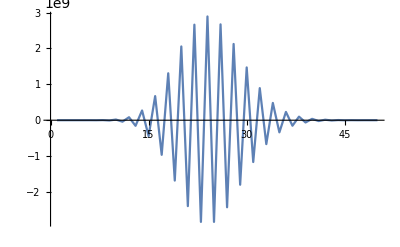

```mathematica
ListLinePlot[Table[(Series[Exp[ λ expArg],{λ,0,n}]//Normal)/.λ-> 1/.int[2]->50//N,{n,1,50}],PlotRange->Full]
```

### Section 4 DBIVA

#### eq (4.58)

```mathematica
fullIntegrand=1/2Nv vectorCut1loop -Nf fermCut1loop +Ns scalarCut1loop/.μ-> MU//Expand;
```

```mathematica
fullIntegral=(integrateBubble[fullIntegrand,l[1],k[1]+k[2]]/.MU-> μ//lorentzContract)/.k[a_]:>k[a,0];
```

Plug in different values for (NF, NS, NV) to check results:

```mathematica
With[{NV= 1,NF=2,NS=2},Solve[(#==0)&/@(fullIntegral-(a[1]F[1,2]F[3,4]s[1,2]^2+a[2]F[1,2]F[1,3]s[1,3]s[2,3]+a[3]F[1,3,2,4]s[1,2]^2+a[4]F[1,3,2,4]s[1,3]s[2,3]+a[5](F[1,3]F[2,4]+F[1,4]F[2,3])s[1,2]^2+a[6](F[1,3]F[2,4]+F[1,4]F[2,3])s[1,3]s[2,3]+ a[7](F[1,2,3,4]+F[1,2,4,3])s[1,2]^2+a[8](F[1,2,3,4]+F[1,2,4,3])s[1,3]s[2,3])/.k[a_,0]:>k[a]/.kinBasis//getSystem),a/@Range@8]/.{Nv-> NV,Nf-> NF,Ns-> NS}/.Ds->6/.g[6]-> 4//Simplify]//First//TableForm
```

a[1]→-int[2]
a[2]→0
a[3]→int[2]
a[4]→0
a[5]→-int[2]
a[6]→0
a[7]→int[2]
a[8]→0

#### eq (4.62) - (4.65)

Wilson coefficient expressions from one-loop integrals.

```mathematica
G[a_]:=2(blp[k[a-1,0],k[a,0]]blp[k[a+1,0],ϵ[k[a,0]]]-blp[k[a+1,0],k[a,0]]blp[k[a-1,0],ϵ[k[a,0]]])/.{k[5,0]-> k[1,0],k[0,0]-> k[4,0]};
```

```mathematica
F2F2[x_,y_]:=nS["dd1"]^x nS["dd2"]^y F[1,2]F[3,4]+nT["dd1"]^x nT["dd2"]^y F[1,4]F[3,2]+nU["dd1"]^x nU["dd2"]^y F[1,3]F[2,4];
```

```mathematica
F4[x_,y_]:=nS["dd1"]^x nS["dd2"]^y F[1,3,2,4]+nT["dd1"]^x nT["dd2"]^y F[1,2,4,3]+nU["dd1"]^x nU["dd2"]^y F[1,2,3,4];
```

```mathematica
stF3=(F2F2[0,2]-G[1]G[2]G[3]G[4])/(s[1,2]s[1,3]s[1,4])/.k[a_,0]:>k[a]/.kinBasis//Expand//Simplify;
```

```mathematica
F3[x_,y_]:=(s[1,2]s[1,3]s[1,4]/8)^x((s[1,2]^2+s[1,3]^2+s[1,4]^2)/8)^y stF3;
```

Plug in different values for (NF, NS, NV) to check results:

```mathematica
With[{NF=1,NS=0,NV=0},Solve[(#==0)&/@(Series[fullIntegral+(fullIntegral/.Thread[{k[2,0],k[3,0],k[4,0]}-> {k[3,0],k[4,0],k[2,0]}])+(fullIntegral/.Thread[{k[2,0],k[3,0],k[4,0]}-> {k[4,0],k[2,0],k[3,0]}])-a[F2F2,2,0]F2F2[2,0]-a[F2F2,0,1]F2F2[0,1]-a[F4,0,1]F4[0,1]-a[F4,2,0]F4[2,0]/.k[a_,0]:>k[a]/.kinBasis/.g[Ds]-> 2/.Ds-> 4-2ϵ/.{Ns-> NS,Nv-> NV,Nf-> NF},{ϵ,0,1}]//Normal//getSystem//Expand),{a[F2F2,2,0],a[F2F2,0,1],a[F4,2,0],a[F4,0,1]}]]//Normal//FullSimplify//First//TableForm
```

a[F2F2,2,0]→-1/75 (15+ϵ) int[2]
a[F2F2,0,1]→-1/3 ϵ int[2]
a[F4,2,0]→1/150 (15-19 ϵ) int[2]
a[F4,0,1]→-1/25 (5+2 ϵ) int[2]

#### eq (4.66)

D-dimensional expressions for all-plus

```mathematica
With[{NF=0,NS=0,NV=1},(evaluateIn4D[fullIntegral/(s[1,2]^2 sb[k[1,0],k[2,0]]^2sb[k[3,0],k[4,0]]^2int[2])/.k[a_]:>k[a,0],{p,p,p,p},constructOnShellNull[4,4]]//Simplify//Rationalize)/.{Ns-> NS,Nv-> NV,Nf-> NF}]//Simplify
```

((-4+Ds) (-2+Ds)^2)/(32 (-1+Ds^2))

#### eq (4.74)

All-plus two-loop Born-Infeld

```mathematica
dubBubbleAllPlus12=Series[evaluateIn4D[(fullIntegral2Bub)/(sb[k[1,0],k[2,0]]^2sb[k[4,0],k[3,0]]^2 (s[1,2]^4)),{p,p,p,p},vectors[1]]/.Ds-> 4-2ϵ//Together//Rationalize//FullSimplify,{ϵ,0,1}]
```

-37/150 int[2]^2 ϵ+O[ϵ]^2

```mathematica
ostrichAllPlus12=Series[(evaluateIn4D[#/(s[1,2]^3 (sb[k[1,0],k[2,0]]^2sb[k[3,0],k[4,0]]^2)) ,{p,p,p,p},vectors[2]] int["ost"]/(int[3,1-Ds/2]int[2]))/.Ds-> 4-2ϵ,{ϵ,0,1}]&/@fullIntegral2loopDunce//Rationalize
```

-4/75 int[ost] ϵ+O[ϵ]^2

```mathematica
ostrichAllPlus34=ostrichAllPlus12
```

-4/75 int[ost] ϵ+O[ϵ]^2

Full s-channel contribution is then:

```mathematica
(1/4(dubBubbleAllPlus12)+1/2(ostrichAllPlus12+ostrichAllPlus34)//Normal)/.int["ost"]-> int[2]^2 (Series[(triangleI[1,ϵ-1,1])/(Sij bubbleI[1,1])/.Ds->4-2ϵ,{ϵ,0,0}]//Normal)
```

-29/600 ϵ int[2]^2

#### eq (4.76)

one-minus two-loop Born-Infeld

```mathematica
dubBubbleOneMinus12=Series[evaluateIn4D[(fullIntegral2Bub)/(ab[k[1,0],k[2,0]]^2sb[k[3,0],k[2,0]]^2sb[k[4,0],k[2,0]]^2 (s[1,2]^3)),{m,p,p,p},vectors[1]]/.Ds-> 4-2ϵ//Together//Rationalize//FullSimplify,{ϵ,0,2}]
```

0

```mathematica
ostrichOneMinus12=Series[(evaluateIn4D[#/(ab[k[1,0],k[2,0]]^2sb[k[3,0],k[2,0]]^2sb[k[4,0],k[2,0]]^2 (s[1,2]^2)) ,{m,p,p,p},vectors[2]] int["ost"]/(int[3,1-Ds/2]int[2]))/.Ds-> 4-2ϵ,{ϵ,0,1}]&/@fullIntegral2loopDunce//Rationalize
```

O[ϵ]^2

```mathematica
ostrichOneMinus34=Series[(evaluateIn4D[#/(sb[k[1,0],k[2,0]]^2sb[k[3,0],k[2,0]]^2ab[k[4,0],k[2,0]]^2 (s[1,2]^2)) ,{p,p,p,m},vectors[2]] int["ost"]/(int[3,1-Ds/2]int[2]))/.Ds-> 4-2ϵ,{ϵ,0,1}]&/@fullIntegral2loopDunce//Rationalize
```

-8/75 int[ost] ϵ+O[ϵ]^2

The full s-channel contribution is then:

```mathematica
(1/4(dubBubbleOneMinus12)+1/2(ostrichOneMinus12+ostrichOneMinus34)//Normal)/.int["ost"]-> int[2]^2 (Series[(triangleI[1,ϵ-1,1])/(Sij bubbleI[1,1])/.Ds->4-2ϵ,{ϵ,0,0}]//Normal)
```

1/75 ϵ int[2]^2

#### eq (4.77)

split-helicity two-loop Born-Infeld

```mathematica
dubBubbleMHVSame12=Series[evaluateIn4D[(fullIntegral2Bub)/(ab[k[1,0],k[2,0]]^2sb[k[3,0],k[4,0]]^2 (s[1,2]^4)),{m,m,p,p},vectors[1]]/.Ds-> 4-2ϵ//Together//Rationalize//FullSimplify,{ϵ,0,0}]
```

int[2]^2+O[ϵ]^1

```mathematica
dubBubbleMHVSplit12=Series[evaluateIn4D[(fullIntegral2Bub)/(ab[k[1,0],k[4,0]]^2sb[k[3,0],k[2,0]]^2 (s[1,2]^4)),{m,p,p,m},vectors[1]]/.Ds-> 4-2ϵ//Together//Rationalize//FullSimplify,{ϵ,0,0}]
```

(4 int[2]^2)/25+O[ϵ]^1

```mathematica
ostrichMHVSame12=Series[(evaluateIn4D[#/(ab[k[1,0],k[2,0]]^2sb[k[3,0],k[4,0]]^2 (s[1,2]^3)) ,{m,m,p,p},vectors[2]] int["ost"]/(int[3,1-Ds/2]int[2]))/.Ds-> 4-2ϵ,{ϵ,0,0}]&/@fullIntegral2loopDunce//Rationalize
```

-(4 int[ost])/15+O[ϵ]^1

```mathematica
ostrichMHVSplit12=Series[(evaluateIn4D[#/(ab[k[1,0],k[4,0]]^2sb[k[3,0],k[2,0]]^2 (s[1,2]^3)) ,{m,p,p,m},vectors[2]] int["ost"]/(int[3,1-Ds/2]int[2]))/.Ds-> 4-2ϵ,{ϵ,0,0}]&/@fullIntegral2loopDunce//Rationalize
```

-(22 int[ost])/75+O[ϵ]^1

For the contributions with (--|++) only the s-channel contributes:

```mathematica
(1/4(dubBubbleMHVSame12)+1/2(ostrichMHVSame12+ostrichMHVSame12)//Normal)/.int["ost"]-> int[2]^2 (Series[(triangleI[1,ϵ-1,1])/(Sij bubbleI[1,1])/.Ds->4-2ϵ,{ϵ,0,0}]//Normal)
```

(19 int[2]^2)/60

For the contributions with (-+|+-) only the t-channel and u-channel contribute:

```mathematica
(1/4(dubBubbleMHVSplit12)+1/2(ostrichMHVSplit12+ostrichMHVSplit12)//Normal)/.int["ost"]-> int[2]^2 (Series[(triangleI[1,ϵ-1,1])/(Sij bubbleI[1,1])/.Ds->4-2ϵ,{ϵ,0,0}]//Normal)
```

(17 int[2]^2)/150

#### eq (4.95)

split-helicity two-loop N=4 DBIVA

```mathematica
dubBubble12=int[2]^2;
```

```mathematica
ostrich12=2int["ost"]/3;
ostrich34=2int["ost"]/3;
```

```mathematica
(1/4(dubBubble12)+1/2(ostrich12+ostrich34)//Normal)/.int["ost"]-> int[2]^2 (Series[(triangleI[1,ϵ-1,1])/(Sij bubbleI[1,1])/.Ds->4-2ϵ,{ϵ,0,0}]//Normal)
```

int[2]^2/12

### Section 5

#### eq (5.24)

Define the operators needed for anomaly cancellation:

```mathematica
T4p=2F2F2[2,0]-F4[2,0]-2F2F2[0,1]/.k[a_,0]:>k[a];
```

```mathematica
t8F4=2(F[1,3,2,4]+F[1,2,4,3]+F[1,2,3,4]-F[1,2]F[3,4]-F[1,3]F[4,2]-F[1,4]F[2,3]);
```

All-plus counterterm T4+ with t8F4 in all-plus sector

```mathematica
sChannelIntegral["T4p","t8F4"]=integrateBubble[((T4p/.Thread[(k/@Range@4)-> {k[1],k[2],l[1],l[2]}])(t8F4/.Thread[(k/@Range@4)-> {-l[1],-l[2],k[3],k[4]}])//Expand//kitchenSinkStateSum)/.l[2]->-l[1]-k[1]-k[2]/.bubRules1loop//Expand,l[1],k[1]+k[2]]/.kinBasis;
```

```mathematica
Series[evaluateIn4D[sChannelIntegral["T4p","t8F4"]/(s[1,2]^4sb[k[1,0],k[2,0]]^2sb[k[3,0],k[4,0]]^2)/.k[a_]:>k[a,0],{p,p,p,p},constructOnShellNull[4,4]]/.{Ds-> 4-2ϵ},{ϵ,0,1}]//Rationalize//Normal
```

(7 int[2])/10+79/300 ϵ int[2]

#### eq (5.26)

All-plus counterterm with t8F4 in all-plus D-dim

```mathematica
sChannelIntegral["Oev","t8F4"]=integrateBubble[((Oev/.Thread[(k/@Range@4)-> {k[1],k[2],l[1],l[2]}])(t8F4/.Thread[(k/@Range@4)-> {-l[1],-l[2],k[3],k[4]}])//Expand//kitchenSinkStateSum)/.l[2]->-l[1]-k[1]-k[2]/.bubRules1loop//Expand,l[1],k[1]+k[2]]/.kinBasis;
```

```mathematica
evaluateIn4D[sChannelIntegral["Oev","t8F4"]/(s[1,2]^4sb[k[1,0],k[2,0]]^2sb[k[3,0],k[4,0]]^2)/.k[a_]:>k[a,0],{p,p,p,p},constructOnShellNull[4,4]]//Simplify//Together//Rationalize//FullSimplify
```

-((-4+Ds) (4+(-7+Ds) Ds) int[2])/(32 (-1+Ds^2))

#### eq (5.27)

All-plus counterterm with t8F4 in one-minus D-dim

```mathematica
sChannelIntegral["Oev","t8F4"]=integrateBubble[((Oev/.Thread[(k/@Range@4)-> {k[1],k[2],l[1],l[2]}])(t8F4/.Thread[(k/@Range@4)-> {-l[1],-l[2],k[3],k[4]}])//Expand//kitchenSinkStateSum)/.l[2]->-l[1]-k[1]-k[2]/.bubRules1loop//Expand,l[1],k[1]+k[2]]/.kinBasis;
```

```mathematica
evaluateIn4D[sChannelIntegral["Oev","t8F4"]/(s[1,2]^3ab[k[4,0],k[3,0]]^2sb[k[3,0],k[2,0]]^2sb[k[3,0],k[1,0]]^2)/.k[a_]:>k[a,0],{p,p,p,m},constructOnShellNull[4,4]]//Simplify//Together//Rationalize//FullSimplify
```

-((-4+Ds) (2+Ds) int[2])/(8 (-1+Ds^2))

#### eq (5.29)

Computing the Wilson coefficient of evanescent operator a_i/(D-4) (i.e. the coefficient that cancels of the (-+++) 1/ϵ-anomaly at two-loop)

```mathematica
Solve[1/75(Ds-4)/2 int[2]^2==1/30 int[2] a[ev]1/2evaluateIn4D[sChannelIntegral["Oev","t8F4"]/(s[1,2]^3ab[k[4,0],k[3,0]]^2sb[k[3,0],k[2,0]]^2sb[k[3,0],k[1,0]]^2)/.k[a_]:>k[a,0],{p,p,p,m},constructOnShellNull[4,4]]//Simplify//Together//Rationalize//FullSimplify,a[ev]] /.Ds-> 4
```

{{a[ev]→-8}}

#### eq (5.31)

This is the single evanescent operator defined in terms of our D-dimensional basis at (α')^6

```mathematica
OevAprime6=F2F2[4,0]-2F2F2[2,1]+F2F2[0,2]+F4[2,1]-F4[0,2]/.k[a_,0]:>k[a];
```

```mathematica
evaluateIn4D[OevAprime6/.k[a_]:>k[a,0],{p,p,p,p},constructOnShellNull[4,4]]//Chop
```

0

```mathematica
evaluateIn4D[OevAprime6/.k[a_]:>k[a,0],{m,p,p,p},constructOnShellNull[4,4]]//Chop
```

0

```mathematica
evaluateIn4D[OevAprime6/.k[a_]:>k[a,0],{m,m,p,p},constructOnShellNull[4,4]]//Chop
```

0

#### eq (5.52)

Hilbert series of gen D

```mathematica
Series[((x+2)(x+1)+x^2)/((x-1)^2(x+1)(x^2+x+1)),{x,0,10}]
```

2+3 x+4 x^2+5 x^3+7 x^4+7 x^5+9 x^6+10 x^7+11 x^8+12 x^9+14 x^10+O[x]^11

And Hilbert series for gen D

```mathematica
Series[((x+2)(x+1)-x^3)/((x-1)^2(x+1)(x^2+x+1)),{x,0,10}]
```

2+3 x+3 x^2+4 x^3+6 x^4+5 x^5+7 x^6+8 x^7+8 x^8+9 x^9+11 x^10+O[x]^11

#### eq (5.53)

And Hilbert series for evanescent operators

```mathematica
Series[((x+2)(x+1)+x^2)/((x-1)^2(x+1)(x^2+x+1))-((x+2)(x+1)-x^3)/((x-1)^2(x+1)(x^2+x+1)),{x,0,10}]
```

x^2+x^3+x^4+2 x^5+2 x^6+2 x^7+3 x^8+3 x^9+3 x^10+O[x]^11

## Follow up to Referee clarifications

### Find generating functions (for symmetric and perm invariant rings)

```mathematica
symInvariantList={1,1,2,2,3,3,4,4,5,5,6,6,7,7,8,8};
permInvariantList={1,0,1,1,1,1,2,1,2,2,2,2,3,2,3,3};
```

Note that the symmetric invariants repeats every 2 entries, and the perm invariants repeat every 6 entries.

One can simply call FindGeneratingFunction[list___], or consult OEIS

```mathematica
FindGeneratingFunction[symInvariantList,α]==1/((α-1)^2(α+1))
```

True

```mathematica
FindGeneratingFunction[permInvariantList,α]==1/((α-1)^2(α+1)(α^2+α+1))//FullSimplify
```

True

```mathematica
Series[1/((α-1)^2(α+1)(α-Exp[ 2I Pi/3])(α-Exp[- 2I Pi/3])),{α,0,12}]//FullSimplify
```

1+α^2+α^3+α^4+α^5+2 α^6+α^7+2 α^8+2 α^9+2 α^10+2 α^11+3 α^12+O[α]^13

```mathematica
uptoEightPointKinList=Table[graphKinRules[massiveGraphs[0&/@Range@i]]/.k[a_,0]:>k[a],{i,3,8}];
```